```mathematica
(* Copyright 2013 Thomas Trogdon *)
(* This software is distributed under the terms of the GNU General Public License *)(*why this computation of norming constants is hard?*)
```

```mathematica
Quit[];
```

```mathematica
AppendTo[$Path,NotebookDirectory[]];
<<RiemannHilbert`;
<<ISTPackage`;
<<ISTPackage`mySGlab`;
```

```mathematica
(*Solving u_tt-u_xx+sin u=0    lab coord *)
```

## Exact solution

```mathematica
(*"1 soliton" solution from wiki, kink solution*)
pm=2;pv=2;pd=3;pg=Sqrt[1/(1-pv^2)];
sol1[x_,t_]:=4*ArcTan[Exp[pm*x-Sqrt[pm^2-1]*t]];(*kink sol for utt-uxx+sin u=0*)
FullSimplify[D[sol1[x,t],t,t]-D[sol1[x,t],x,x]+Sin[sol1[x,t]]]
Manipulate[Plot[sol1[x,t],{x,-10,10},PlotRange->All],{t,-2,2}]
```

0

```mathematica
pm=2;pv=2;pd=3;pg=Sqrt[1/(1-pv^2)];
sol2[x_,t_]:=4*ArcTan[Exp[pm*(x+t)-Sqrt[pm^2-1]*(x-t)]];(*kink sol for uxt=sin u*)
FullSimplify[D[sol2[x,t],x,t]-Sin[sol2[x,t]]]
Manipulate[Plot[sol2[x,t],{x,-50,50},PlotRange->All],{t,-2,2}]
```

0

```mathematica
pt=1;pa=Cos[pt];pb=Sin[pt];
sol3[x_,t_]:=4*ArcTan[pb/pa*Cos[pa*(t)]*Sech[pb*(x)]];(* sitting breather sol for utt-uxx+sin u=0*)
FullSimplify[D[sol3[x,t],t,t]-D[sol3[x,t],x,x]+Sin[sol3[x,t]]]
Manipulate[Plot[sol3[x,t],{x,-20,20},PlotRange->{-3,3}],{t,-5,5}]
```

0

```mathematica
pt=1;pa=Cos[pt];pb=Sin[pt];
sol3[x_,t_]:=4*ArcTan[pb/pa*Cos[pa*(x-t)]*Sech[pb*(x+t)]];(* moving breather sol for uxt=sin u*)
FullSimplify[D[sol3[x,t],x,t]-Sin[sol3[x,t]]]
Manipulate[Plot[sol3[x,t],{x,-20,20},PlotRange->{-3,3}],{t,-5,5}]
```

0

```mathematica
pt=1;pa=Cos[pt];pb=Sin[pt];
eta=1/2;
sol3[x_,t_]:=4*ArcTan[Exp[(eta/2+1/2/eta)*x+(eta/2-1/2/eta)*t]];(* kink sol for utt-uxx+sin u=0*)
FullSimplify[D[sol3[x,t],t,t]-D[sol3[x,t],x,x]+Sin[sol3[x,t]]]
Manipulate[Plot[sol3[x,t],{x,-20,20},PlotRange->{-1,8}],{t,-10,10}]
```

0

```mathematica
theta=Pi/2-0.5;
eta=Exp[I theta];
omega=-Re[eta];
sol3[x_,t_]:=4*ArcTan[Sqrt[(1-omega^2)/omega^2]*Cos[omega*(t)]*Sech[Sqrt[1-omega^2]*(x)]];(*sitting breather sol for utt-uxx+sin u=0*)
Manipulate[Plot[sol3[x,t],{x,-20,20},PlotRange->{-5,5}],{t,-5,50}]
```

```mathematica
D[sol3[x,t],t,t]-D[sol3[x,t],x,x]+Sin[sol3[x,t]]/.x->1/.t->10
```

-1.249×10^-16

```mathematica
(*A moving breather obtained from Lorentz transform on sitting breather*)
c0=1;u=1;v=0.5;
sol5[x_,t_]:=4*ArcTan[c0/u*Cos[u/c0/(Sqrt[1+u^2/c0^2])*(t-v*x/c0^2)/Sqrt[1-v^2/c0^2]]*Sech[1/c0/(Sqrt[1+u^2/c0^2])*(x-v*t)/Sqrt[1-v^2/c0^2]]];(* moving breather sol for utt-uxx+sin u=0*)
freq=u/c0/Sqrt[1+u^2/c0^2]
D[sol5[x,t],t,t]-D[sol5[x,t],x,x]+Sin[sol5[x,t]]/.x->0/.t->1.
 Manipulate[Plot[sol5[x,t],{x,-10,20},PlotRange->{-4,4}],{t,0,10}]
```

```mathematica
(*Check Lax Pair*)
X[x_,t_,z_]:=({{-I z, -D[u[x,t],x]/2}, {D[u[x,t],x]/2, I z}});
```

```mathematica
T[x_,t_,z_]:=({{I*Cos[u[x,t]] /4/z, I*Sin[u[x,t]]/4/z}, {I*Sin[u[x,t]] /4/z, -I*Cos[u[x,t]] /4/z}});
```

```mathematica
D[X[x,t,z],t]-D[T[x,t,z],x]+X[x,t,z].T[x,t,z]-T[x,t,z].X[x,t,z]
```

{{0,1/2 Sin[u[x,t]]-1/2 u^(1,1)[x,t]},{-1/2 Sin[u[x,t]]+1/2 u^(1,1)[x,t],0}}

```mathematica
(*Approx 2 kink*)
x0=5;k=Sqrt[4/3];
sol3[x_,t_]:=4ArcTan [Exp[k(x+x0-0.5t)]]-4ArcTan [Exp[k(x-x0+0.5t)]];
Manipulate[TablePlot[Cos[sol3[x,t]],{x,-20,20,0.2},PlotRange->{-2Pi,2Pi}],{t,0,20,0.5}]
(*sol3[x_,t_]:=5Sech[x^2];*)
(*sol3[x_,t_]:=9Sech[x+0.7t];*)
```

## Normal Reflection Coefficient

```mathematica
(*q[x_]:=1*Sech[x]^4;
qt[x_]:=0;
qx[x_]=D[q[x],x];
q[_?InfinityQ]:=0.;    (* PatternTest: q[infinity] gets replaces by 0 *)
qt[_?InfinityQ]:=0.;*)
```

```mathematica
(*this is the case suffering a branch cut thing for H?*)
q[x_]:=2*ArcCos[Tanh[x]];
qt[x_]:=0*x;
(*qx[x_]=Simplify[D[q[x],x]]/.Underflow[]->0/.Indeterminate->0.;*)
qx[x_]=-2 Sech[x]/.Underflow[]->0/.Indeterminate->0.;
(*q[_?InfinityQ]:=0.;    (* PatternTest: q[infinity] gets replaces by 0 *)*)
qt[_?InfinityQ]:=0.;
```

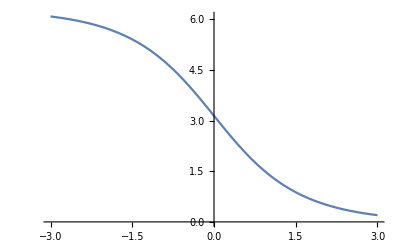

```mathematica
Plot[q[x],{x,-3,3}]
```

```mathematica
q[15.]
```

1.22371×10^-6

```mathematica
LL=9.;
LL=15.;
Clear[H];
H[k_]:=H[k]=ScatteringMatrixFiniteSG[q,qt,40,LL][k];
H[_?InfinityQ]=Round[H[1/0.0001]];
H[_?PossibleZeroQ]=Round[H[0.0001]];
aa//Clear;bb//Clear;
aa[k_]:=aa[k]=H[k][[1,1]];
bb[k_]:=bb[k]=H[k][[2,1]];
AA[k_]:=AA[k]=H[k][[2,2]];
BB[k_]:=BB[k]=H[k][[1,2]];
(*(*Need high accuracy of H for solitons*)
H1=ScatteringMatrixFiniteSG[q,qt,200,LL];
H1[_?InfinityQ]=Round[H[1/0.0001]];
H1[_?PossibleZeroQ]=Round[H[0.0001]];
aa1//Clear;bb1//Clear;
aa1[k_]:=aa1[k]=H1[k][[1,1]];
bb1[k_]:=bb1[k]=H1[k][[2,1]];*)
H[1-0.00001]
H[1+0.00001]
```

{{9.99253×10^-6+1. ⅈ,6.03911×10^-7+0. ⅈ},{6.03911×10^-7+2.22045×10^-16 ⅈ,-9.99253×10^-6+1. ⅈ}}

{{9.99243×10^-6-1. ⅈ,-6.03911×10^-7+1.66533×10^-16 ⅈ},{-6.03911×10^-7-1.11022×10^-16 ⅈ,-9.99243×10^-6-1. ⅈ}}

```mathematica
SetAttributes[q,Listable];SetAttributes[qt,Listable];SetAttributes[qx,Listable];
```

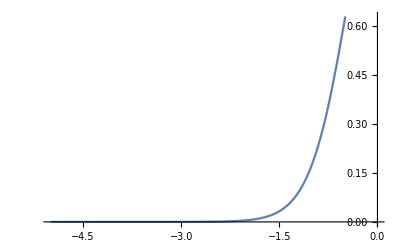
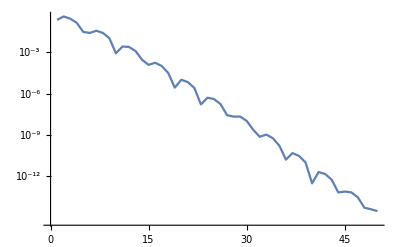
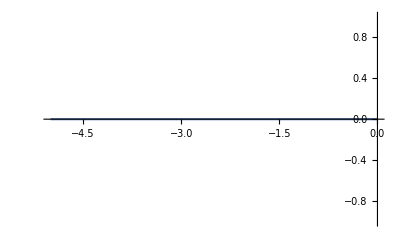
{-Graphics-,3.29725×10^-8,-Graphics-,-Graphics-,-Graphics-,0}

```mathematica
{Plot[Fun[q,Line[{-LL,0}],50][x],{x,-LL,0}],q[-LL],Fun[q,Line[{-LL,0}],50]//DCTPlot,Plot[Fun[qt,Line[{-LL,0}],50][x],{x,-LL,0},PlotRange->All],Fun[qt,Line[{-LL,0}],50]//DCTPlot,qt[-LL]}
```

```mathematica
Poles0=LocatePolesSG[q,qx,qt,0.25,100]
```

{}

```mathematica
Poles = {};
For[i=1,i≤Length[Poles0],i++,
If[Abs[aa[Poles0[[i]]]]<0.2, 
Poles=Join[Poles,{Poles0[[i]]}];
];
];
```

```mathematica
Poles
Abs[Poles]
```

{}

{}

```mathematica
H/@ Poles0
```

{}

```mathematica
H1/@Poles0(*The warning messages may due to calculation of b A outside the region of decaying*)
```

{}

```mathematica
H[1-0.00001]-H[1+0.00001]
```

{{1.×10^-10+2. ⅈ,1.20782×10^-6-1.66533×10^-16 ⅈ},{1.20782×10^-6+3.33067×10^-16 ⅈ,-1.×10^-10+2. ⅈ}}

```mathematica
H[(1+I)*(0.01)]
```

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{0.997159-0.00284034 ⅈ,0.00568295+0.00568068 ⅈ,-0.00568295-0.00568068 ⅈ,0.00568295+0.00568068 ⅈ,-0.00568295-0.00568068 ⅈ,0.00568295+0.00568068 ⅈ,-0.00568295-0.00568068 ⅈ,0.00568295+0.00568068 ⅈ,«35»,0.00568295+0.00568068 ⅈ,-0.00568295-0.00568068 ⅈ,0.00568295+0.00568068 ⅈ,-0.00568295-0.00568068 ⅈ,0.00568295+0.00568068 ⅈ,-0.00568295-0.00568068 ⅈ,0.00568295+0.00568068 ⅈ,«150»},«49»,«150»} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{1.+3.97064×10^-7 ⅈ,-5.34481×10^-6+5.34481×10^-6 ⅈ,-0.0000101875+0.0000101875 ⅈ,-0.0000158157+0.0000158157 ⅈ,-0.0000204283+0.0000204283 ⅈ,-0.0000258784+0.0000258784 ⅈ,-0.000030066+0.000030066 ⅈ,-0.0000348184+0.0000348184 ⅈ,-0.0000379539+0.0000379539 ⅈ,«34»,-1.64452×10^-14+1.64452×10^-14 ⅈ,-5.38023×10^-15+5.38023×10^-15 ⅈ,-1.758×10^-15+1.758×10^-15 ⅈ,-5.67064×10^-16+5.67064×10^-16 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,«150»},{«1»},«47»,{«1»},«150»} may contain significant numerical errors.

{{0.996879+0.0030891 ⅈ,0.000319008+0.000335455 ⅈ},{0.0000742521-0.000489624 ⅈ,-1.00312+0.00310831 ⅈ}}

```mathematica
H[1000]
```

{{1.-0.000311012 ⅈ,1.03434×10^-16-5.81493×10^-16 ⅈ},{-6.69892×10^-16+3.83113×10^-17 ⅈ,-1.-0.000311012 ⅈ}}

### test cond for foward scattering

#### outside unit circle v2 by integrate the z-1/z part (ignore the 1/w in Q now)

```mathematica
el=20;
n=100;
CME[x_]:=Chop[x,$MachineEpsilon];

 qf=Fun[q,Line[{-el,0}],n]; (*Forward scattering*)
qtf=Fun[qt,Line[{-el,0}],n];
qxf=qf';(*assume the diff is spectral*)
qfb=Fun[q,Line[{0,el}],n];
qtfb=Fun[qt,Line[{0,el}],n];
qxfb=qfb';
xf=Fun[#&,Line[{-el,0}],n];
xfb=Fun[#&,Line[{0,el}],n];

z=(w-1/w)/4;
w1=1;
Dm=DerivativeMatrix[qf];      (*this gives the chebyshev differentiation matrix*)
IIm=ReduceDimensionIntegrateMatrix[qf];
id=IdentityMatrix[n];
Q11 = DiagonalMatrix[(I/4/w*(Cos[qf]-1))  //Values];
Q12 = DiagonalMatrix[(I/4/w*Sin[qf]-1/4*(qtf+qxf))  //Values];
Q21 = DiagonalMatrix[(I/4/w*Sin[qf]+1/4*(qtf+qxf)) //Values];
Q22 = DiagonalMatrix[-(I/4/w*(Cos[qf]-1)) //Values];
Qb11 = DiagonalMatrix[(I/4/w*(Cos[qfb]-1))  //Values];
Qb12 = DiagonalMatrix[(I/4/w*Sin[qfb]-1/4*(qtfb+qxfb))  //Values];
Qb21 = DiagonalMatrix[(I/4/w*Sin[qfb]+1/4*(qtfb+qxfb)) //Values];
Qb22 = DiagonalMatrix[-(I/4/w*(Cos[qfb]-1)) //Values];

Jσ3=BlockMatrix[{{0*id,0},{0,-2I IIm}}];
Jσ31=BlockMatrix[{{2I IIm,0},{0,0*id}}];
Jσ3b=BlockMatrix[{{0*id,0},{0,-2I IImb}}];
Jσ31b=BlockMatrix[{{2I IImb,0},{0,0*id}}];
A=BlockMatrix[{{id-IIm.Q11,-IIm.Q12},{-IIm.Q21,id-IIm.Q22}}];
Ab=BlockMatrix[{{id-IImb.Qb11,-IImb.Qb12},{-IImb.Qb21,id-IImb.Qb22}}];

On[LinearSolve::luc];
lhs=A+ z*Jσ3;
rhs = Join[IIm.Diagonal[Q11],IIm.Diagonal[Q21]];
Print["Linear solve 1 cond=",Max[SingularValueList[lhs,Tolerance->0]]/Min[SingularValueList[lhs,Tolerance->0]]];
(*Print[SingularValueList[lhs//CME]];*)
illlhs=lhs;
ans0a = LinearSolve[lhs//CME,rhs//CME];

expzx=DiagonalMatrix[(Exp[2*I*z*xf])//Values];
iexpzx=DiagonalMatrix[(Exp[-2*I*z*xf])//Values];
expzxb=DiagonalMatrix[(Exp[2*I*z*xfb])//Values];
iexpzxb=DiagonalMatrix[(Exp[-2*I*z*xfb])//Values];

A=BlockMatrix[{{id-iexpzx.IIm.expzx.Q11,-iexpzx.IIm.expzx.Q12},{-IIm.Q21,id-IIm.Q22}}];
lhs=A;
rhs=Join[-iexpzx.IIm.expzx.Diagonal[Q12],-IIm.Diagonal[Q22]];
Print["Linear solve 2 cond=",Max[SingularValueList[lhs,Tolerance->0]]/Min[SingularValueList[lhs,Tolerance->0]]];
ans1a = LinearSolve[lhs//CME,rhs//CME];

Ab=BlockMatrix[{{id-IImb.Qb11,-IImb.Qb12},{-expzx.IImb.iexpzx.Qb21,id-expzx.IImb.iexpzx.Qb22}}];
lhs=Ab;
rhs = Join[IImb.Diagonal[Qb11],expzx.IImb.iexpzx.Diagonal[Qb21]];
Print["Linear solve 3 cond=",Max[SingularValueList[lhs,Tolerance->0]]/Min[SingularValueList[lhs,Tolerance->0]]];
ans2a = LinearSolve[lhs//CME,rhs//CME];

Ab=BlockMatrix[{{id-IImb.Qb11,-IImb.Qb12},{-IImb.Qb21,id-IImb.Qb22}}];
lhs=Ab+ z*Jσ31b;
rhs = Join[IImb.Diagonal[Qb12],IImb.Diagonal[Qb22]];
Print["Linear solve 4 cond=",Max[SingularValueList[lhs,Tolerance->0]]/Min[SingularValueList[lhs,Tolerance->0]]];
ans3a = LinearSolve[lhs//CME,rhs//CME];
```

Linear solve 1 cond=7.90393×10^11

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«150»},«49»,«150»} may contain significant numerical errors.

Linear solve 2 cond=3.03218×10^15

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«150»},«49»,«150»} may contain significant numerical errors.

Linear solve 3 cond=3.03233×10^15

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{1.00004,0.000593851,0.00113144,0.00175338,0.00225388,0.00282649,0.00322441,0.00362439,0.00377643,«34»,4.77519×10^-15,1.37693×10^-15,3.97311×10^-16,0.,0.,0.,0.,«150»},{«1»},«47»,{«1»},«150»} may contain significant numerical errors.

Linear solve 4 cond=7.90391×10^11

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{0.999084,-0.012325,-0.0234996,-0.0365321,-0.0473598,-0.0604589,-0.0712276,-0.0843864,«36»,-0.390008,-0.393259,-0.39359,-0.396049,-0.395585,-0.397247,«150»},«49»,«150»} may contain significant numerical errors.

```mathematica
Max[Abs[ans0-ans0a]]
Max[Abs[ans1-ans1a]]
Max[Abs[ans2-ans2a]]
Max[Abs[ans3-ans3a]]
```

0.

0.0980649

0.0980649

0.

```mathematica
Max[Abs[expzx]]
```

1.3138×10^16

```mathematica
Exp[2*I*z]
```

0.00640933+0. ⅈ

```mathematica
s1={{ans0[[n]]+1,ans1[[n]]},{ans0[[2n]],ans1[[2n]]-1}}
```

{{0.150186,0.379599},{0.413887,-1.84981}}

```mathematica
IIm.Values[qf]
```

```mathematica
Dimensions[A]
```

{400,400}

#### inside unit circle

```mathematica
w=0.2;
Q11 = DiagonalMatrix[(I/4*w*(Cos[qf]-1))  //Values];
Q12 = DiagonalMatrix[(-I/4*w*Sin[qf]-1/4*(qxf-qtf))  //Values];
Q21 = DiagonalMatrix[(-I/4*w*Sin[qf]+1/4*(qxf-qtf)) //Values];
Q22 = DiagonalMatrix[-(I/4*w*(Cos[qf]-1)) //Values];

Jσ3=BlockMatrix[{{0*id,0},{0,-2I IIm}}];
Jσ31=BlockMatrix[{{2I IIm,0},{0,0*id}}];
A=BlockMatrix[{{id+IIm.Q11,+IIm.Q12},{+IIm.Q21,id+IIm.Q22}}];
(*A=BlockMatrix[{{id,0},{0,id}}];*)

z=(w-1/w)/4;
On[LinearSolve::luc];
lhs=A+ z*Jσ3;
rhs = Join[-IIm.Diagonal[Q11],-IIm.Diagonal[Q21]];
Print["Linear solve 1 cond=",Max[SingularValueList[lhs,Tolerance->0]]/Min[SingularValueList[lhs,Tolerance->0]]];
(*Print[SingularValueList[lhs//CME]];*)
illlhs=lhs;
ans0 = LinearSolve[lhs//CME,rhs//CME];

lhs=A+z*Jσ31;
rhs=Join[IIm.Diagonal[Q12],IIm.Diagonal[Q22]];
Print["Linear solve 2 cond=",Max[SingularValueList[lhs,Tolerance->0]]/Min[SingularValueList[lhs,Tolerance->0]]];
ans1 = LinearSolve[lhs//CME,rhs//CME];
```

Linear solve 1 cond=1213.5

Linear solve 2 cond=1213.5

#### inside unit circle with partial integration

```mathematica
xf=Fun[#&,Line[{-el,0}],n];
xfb=Fun[#&,Line[{0,el}],n];
Q11 = DiagonalMatrix[(I/4*w*(Cos[qf]-1))  //Values];
Q12 = DiagonalMatrix[(-I/4*w*Sin[qf]-1/4*(qxf-qtf))  //Values];
Q21 = DiagonalMatrix[(-I/4*w*Sin[qf]+1/4*(qxf-qtf)) //Values];
Q22 = DiagonalMatrix[-(I/4*w*(Cos[qf]-1)) //Values];

Jσ3=BlockMatrix[{{0*id,0},{0,-2I IIm}}];
Jσ31=BlockMatrix[{{2I IIm,0},{0,0*id}}];
A=BlockMatrix[{{id+IIm.Q11,+IIm.Q12},{+IIm.Q21,id+IIm.Q22}}];
(*A=BlockMatrix[{{id,0},{0,id}}];*)

z=(w-1/w)/4;
expzx=DiagonalMatrix[(Exp[2*I*z*xf])//Values];
iexpzx=DiagonalMatrix[(Exp[-2*I*z*xf])//Values];
expzxb=DiagonalMatrix[(Exp[2*I*z*xfb])//Values];
iexpzxb=DiagonalMatrix[(Exp[-2*I*z*xfb])//Values];

On[LinearSolve::luc];
lhs=A+ z*Jσ3;
rhs = Join[-IIm.Diagonal[Q11],-IIm.Diagonal[Q21]];
Print["Linear solve 1 cond=",Max[SingularValueList[lhs,Tolerance->0]]/Min[SingularValueList[lhs,Tolerance->0]]];
(*Print[SingularValueList[lhs//CME]];*)
illlhs=lhs;
ans2 = LinearSolve[lhs//CME,rhs//CME];

A=BlockMatrix[{{id+iexpzx.IIm.expzx.Q11,+iexpzx.IIm.expzx.Q12},{+IIm.Q21,id+IIm.Q22}}];
lhs=A;
rhs=Join[+iexpzx.IIm.expzx.Diagonal[Q12],+IIm.Diagonal[Q22]];
Print["Linear solve 2 cond=",Max[SingularValueList[lhs,Tolerance->0]]/Min[SingularValueList[lhs,Tolerance->0]]];
ans3 = LinearSolve[lhs//CME,rhs//CME];
```

Linear solve 1 cond=1213.5

Linear solve 2 cond=1.252

```mathematica
Max[Abs[ans0-ans2]]
Max[Abs[ans1-ans3]]
```

0.

6.031×10^-15

```mathematica
n=200;
lhs=IdentityMatrix[n]-10*ReduceDimensionIntegrateMatrix[Fun[q&,Line[{0,1}],n]];
Max[SingularValueList[lhs,Tolerance->0]]/Min[SingularValueList[lhs,Tolerance->0]]
```

92646.2

```mathematica
Abs[Eigenvalues[lhs]]
```

```mathematica
Dimensions[lhs]
```

{10,10}

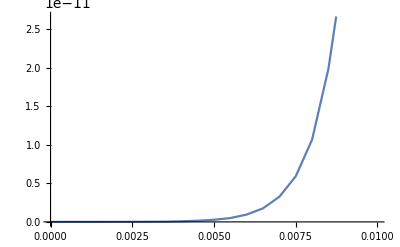

```mathematica
xmax=0.01;
TablePlot[Abs[H[I x][[1,2]]],{x,0,xmax,xmax/20}]
```

```mathematica
H[0.05I]
```

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{0.997468,0.00506313,-0.00506313,0.00506313,-0.00506313,0.00506313,-0.00506313,«37»,-0.00506313,0.00506313,-0.00506313,0.00506313,-0.00506313,0.00506313,«150»},{«1»},«47»,{«1»},«150»} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{0.999996,-0.0000593851,-0.000113144,-0.000175338,-0.000225388,-0.000282649,-0.000322441,-0.000362439,-0.000377643,«33»,-1.63005×10^-15,-4.77519×10^-16,0.,0.,0.,0.,0.,0.,«150»},{«1»},«47»,{«1»},«150»} may contain significant numerical errors.

{{0.985826,-0.0874431},{0.0965624,-1.02294}}

```mathematica
H[0.01I]
```

{{0.997099,-2.24518×10^-11},{1.99465×10^-10,-1.00291}}

```mathematica
H[0.0001I]
```

{{0.999971,3.70612×10^-17},{-5.24502×10^-17,-1.00003}}

```mathematica
zz=0.01I;
H[zz]
```

{{0.997099,-2.24518×10^-11},{1.99465×10^-10,-1.00291}}

```mathematica
Inverse[{{1-Cos[q[0]],-Sin[q[0]]},{-Sin[q[0]],Cos[q[0]]-1+2-2zz^2}}].{{1-Cos[q[0]],-Sin[q[0]]},{-Sin[q[0]],Cos[q[0]]-1}}
```

{{1.+0. ⅈ,-1.83049×10^6+0. ⅈ},{-5.82077×10^-11+0. ⅈ,-1.×10^6+0. ⅈ}}

```mathematica
(Cos[q[0.]]+1)/(Sin[q[0]]^2+(Cos[q[0.]]+1)^2)*Sin[q[0]]
```

0.420735

```mathematica
Simplify[(Cos[x]+1)/(Sin[x]^2+(Cos[x]+1)^2)]
```

1/2

```mathematica
xx=0.;
Sqrt[1/2]*Sin[q[xx]]/Sqrt[1-Cos[q[xx]]]
Sqrt[1/2]*Sqrt[1-Cos[q[xx]]]
```

0.877583

0.479426

```mathematica
Sqrt[1/2]*Sin[q[xx]]/Sqrt[1+Cos[q[xx]]]
-Sqrt[1/2]*Sqrt[1+Cos[q[xx]]]
```

0.479426

-0.877583

```mathematica
Cos[q[0.]/2]
Sin[q[0.]/2]
```

0.877583

0.479426

```mathematica
FullSimplify[Sin[x]/Sqrt[1+cos[x]]]
```

Sin[x]/(√(1+cos[x]))

#### Reflection coeff

```mathematica
Clear[ρ];
Clear[ρ1];(*used to estimate the envolope function h*)
```

```mathematica
ρ1[k_]:=bb[k]/aa[k];
h[k_]:=2*Abs[k]^3/(1+Exp[4*Sqrt[Abs[k]]]);
(*setting h[0]=0 breaks some symmetry since the truncation is determined by the left endpoint of the line segment. In the symmetric case, some magic error cancellation ocurrs with higher accuracy, at least by looking at the magnitude of the imaginary part*)
```

2.0801×10^-12+6.67663×10^-10 ⅈ

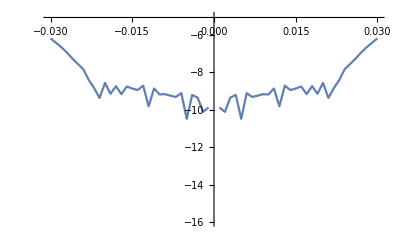
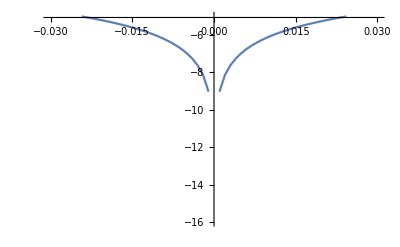
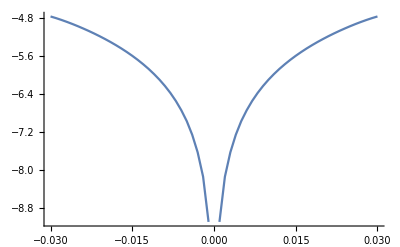

-2.0801×10^-12+6.67663×10^-10 ⅈ

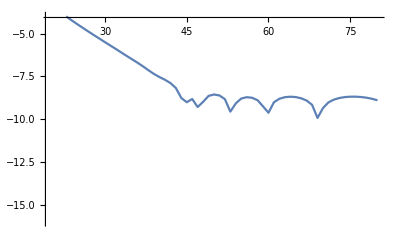
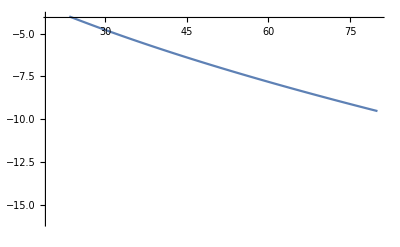
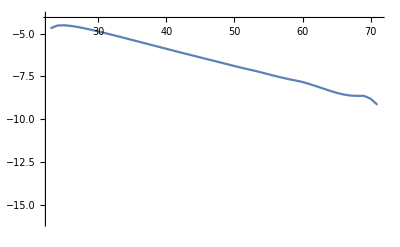

```mathematica
ρ1[0.01]
{TablePlot[Log[10,Abs[ρ1[x]]],{x,-0.03,0.03,0.001},PlotRange->{-16,-5}],TablePlot[Log[10,h[x]],{x,-0.03,0.03,0.001},PlotRange->{-16,-5}],TablePlot[Log[10,h[x]-Abs[ρ1[x]]],{x,-0.03,0.03,0.001}]}
ρ1[100]
{TablePlot[Log[10,Abs[ρ1[x]]],{x,20,80,1},PlotRange->{-16,-4}],TablePlot[Log[10,h[x]],{x,20,80,1},PlotRange->{-16,-4}],TablePlot[Log[10,h[x]-Abs[ρ1[x]]],{x,20,80,1},PlotRange->{-16,-4}]}
```

```mathematica
ρ1[30]
h[30.]
```

-3.32376×10^-8+3.14014×10^-6 ⅈ

0.0000164998

```mathematica
ρ[k_]:=Piecewise[{{0,Abs[k]<0.01}},bb[k]/aa[k]];
ρb[k_]:=Piecewise[{{0,Abs[k]<0.01}},-BB[k]/AA[k]];
(*ρ[k_]:=Abs[k]^2*Sech[Abs[k]^2];*)
rad=0.8;
bigN=120;
smallN=20;
el=60;
ν=0.02;
SetParams[ν,rad,10.^(-6),30,bigN,el];
(*"SetParams[ν,rad,globalTol,smallN,bigN] sets the parameters for the rest of the code:
	ν: half of width of strip of analyticity (In the NLS sense, for sine-Gordon, this determines the Im of (z-1/z)/4 )
	near z=0, this determinse a circle with radius 1/8nu centered at z=I/8nu. In this case, nu< 1/8nu   nu<0.35 
	rad: radius of soliton contours
	globalTol: contour truncation tolerance
	smallN: small number of collocation points
	bigN: big number of collocation points";if no truncations is done, then more points is required to get sufficient accuracy*)
ν=Getnu[];

Setrsamp[h];(*use h for fast truncation*)
Settimeflag[False];
c=SetScatteringData[aa,bb1,ρ,ρb,Poles](*output the norming constant*)
```

{}

```mathematica
ρ[10]
```

-0.00302424+0.0744368 ⅈ

```mathematica
{TablePlot[Abs[bb[x]/aa[x]],{x,-0.1/2,0.1/2,0.001},PlotRange->All],TablePlot[Abs[h[x]]-Abs[ρ[x]],{x,-20,20,0.5},PlotRange->All],
TablePlot[Abs[ρ[x]],{x,20,50,2},PlotRange->All]}
```

$Aborted

```mathematica
hhh=50;
h[hhh]-Abs[ρ[hhh]]
Abs[ρ[500]]
Abs[ρ[40]]
Abs[ρ[30]]
Abs[ρ[25]]
```

0.00274217

0.0538004

1.01657×10^-9

5.23765×10^-8

1.19627×10^-6

## Plotting: timestring outputs relevant computation times and region information

```mathematica
qSGgeneral=NotebookDirectory[]<>"qSGm";(*file name*)
```

```mathematica
(*load qSGm if already calculated*)
qSGm//Clear;
Get["qSGm"];
```

```mathematica
qSG//Clear;
qSG[x_,t_]:=qSG[x,t]=SGAuto[x,t];(*qSG is the solution to the rhp at z=0, the transform qSG[xx,tt].{{1,0},{0,-1}}.Inverse[qSG[xx,tt]] gives the solution q to the sine-Gordon in the form {{cos q, sin q},{sin q, -cos q}}*)
```

```mathematica
myacos[x_]:=Piecewise[{{ArcCos[Re[x[[1,1]]]],ArcSin[Re[x[[1,2]]]]>0},{2Pi-ArcCos[Re[x[[1,1]]]],ArcSin[Re[x[[2,1]]]]≤0}}];
```

```mathematica
xx=30;
tt=0.;
qSG[xx,tt]
timestring
```

{{0.999998-8.66575×10^-21 ⅈ,-0.00216873-1.95965×10^-6 ⅈ},{-0.00216873+1.95965×10^-6 ⅈ,-0.999998+8.66616×10^-21 ⅈ}}

Region: 1 (30.,0.) 1) Construct: 67.5156  1) Solve: 9.89063  2) Construct: 0  2) Solve: 0

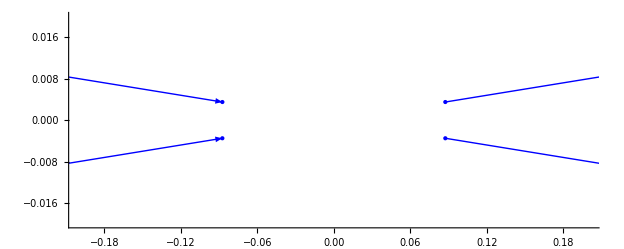

```mathematica
Show[domainOutput,PlotRange->{{-0.2,0.2},{-0.02,0.02}}]
```

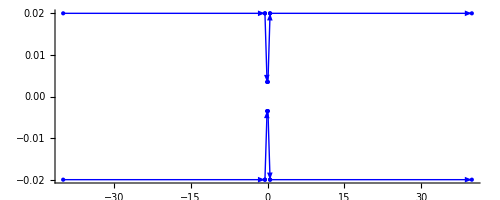

```mathematica
domainOutput
```

```mathematica
Det[qSG[xx,tt]](*should be 1*)
```

-1.-2.04319×10^-23 ⅈ

```mathematica
(*ans=qSG[xx,tt].{{1,0},{0,-1}}.Inverse[qSG[xx,tt]]*)
ans=qSG[xx,tt];
```

```mathematica
Cos[q[xx]]-ans[[1,1]]
Sin[q[xx]]-ans[[1,2]]
Sin[q[xx]]-ans[[2,1]]
(Sin[q[xx]]-ans[[2,1]])/Sin[q[xx]]
(Sin[q[xx]]-ans[[2,1]])/ans[[2,1]]
```

2.35171×10^-6+8.66575×10^-21 ⅈ

0.00216873+1.95965×10^-6 ⅈ

0.00216873-1.95965×10^-6 ⅈ

1.76776×10^48-1.59734×10^45 ⅈ

-1.+1.0842×10^-19 ⅈ

```mathematica
qSG[-0.2,0]
qSG[0.2,0]
```

$Aborted

$Aborted

```mathematica
Cos[q[xx]]-ans[[1,1]]
Sin[q[xx]]-ans[[1,2]]
Sin[q[xx]]-ans[[2,1]]
(Sin[q[xx]]-ans[[2,1]])/Sin[q[xx]]
(Sin[q[xx]]-ans[[2,1]])/ans[[2,1]]
```

6.32149×10^-8-4.64956×10^-13 ⅈ

-4.77783×10^-8+7.11774×10^-12 ⅈ

-4.77753×10^-8-6.41493×10^-12 ⅈ

-5.98853×10^-8-8.04098×10^-12 ⅈ

-5.98853×10^-8-8.04097×10^-12 ⅈ

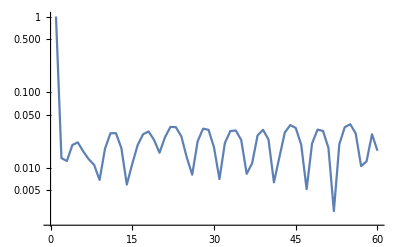
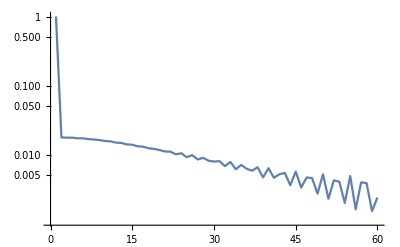
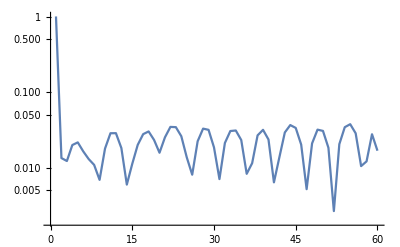
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
DCTPlot/@Grhp1
```

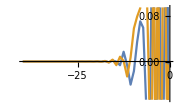

```mathematica
Grhp1[[1]][[1,2]]
```

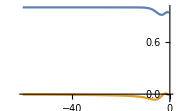

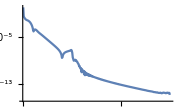

```mathematica
nu1=Sqrt[1/(8ν)^2-(1/(8ν)-ν)^2];
f1=Fun[Φt[xx,tt][#][[1,1]]&,Line[{-el-I*ν,-nu1-I*ν}],300]
DCTPlot[f1]
```

```mathematica
ift[-el]
```

0.+0. ⅈ

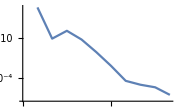

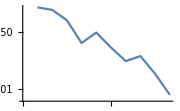

```mathematica
r[k_]:=ρ[k]*cc[ρ[cc[k]]];
r1=Fun[(ρ[#])&,{-2,-0.5}//Line,10];
r2=Fun[(ρ[#])&,{-0.5,0}//Line,10];
DCTPlot[r1]
DCTPlot[r2]
```

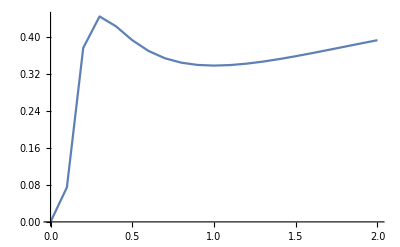

```mathematica
TablePlot[Abs[ρ[ss]],{ss,0,2,0.1}]
```

```mathematica
r[-0.0001]
```

0

```mathematica
ans1=qSG[2,0].{{1,0},{0,-1}}.Inverse[qSG[2,0]];
ans2=qSG[-2,0].{{1,0},{0,-1}}.Inverse[qSG[-2,0]];
Cos[q[2.]]
Sin[q[2.]]
```

0.999988

0.00499152

```mathematica
Cos[q[2]]-ans1[[1,1]]
Sin[q[2]]-ans1[[1,2]]
Sin[q[2]]-ans1[[2,1]]
(Sin[q[2]]-ans1[[2,1]])/Sin[q[2]]
```

-2.24918×10^-9-8.70147×10^-19 ⅈ

4.50616×10^-7-2.70614×10^-16 ⅈ

4.50615×10^-7+6.19292×10^-16 ⅈ

0.0000902762+1.24069×10^-13 ⅈ

```mathematica
Cos[q[-2]]-ans2[[1,1]]
Sin[q[-2]]-ans2[[1,2]]
Sin[q[-2]]-ans2[[2,1]]
(Sin[q[-2]]-ans2[[2,1]])/Sin[q[-2]]
```

-2.24918×10^-9-2.90497×10^-18 ⅈ

4.50615×10^-7+1.46761×10^-15 ⅈ

4.50616×10^-7-3.03556×10^-16 ⅈ

0.0000902763-6.08144×10^-14 ⅈ

```mathematica
qSG[2,0]
qSG[2,0]-qSG[-2,0]
```

{{0.999997-9.82558×10^-20 ⅈ,-0.00249554-1.35308×10^-16 ⅈ},{0.00249554-3.09648×10^-16 ⅈ,0.999997+7.75882×10^-19 ⅈ}}

{{-2.88658×10^-15-5.482×10^-18 ⅈ,4.46417×10^-13-8.69104×10^-16 ⅈ},{1.63036×10^-13-4.61436×10^-16 ⅈ,-1.44329×10^-15-5.22868×10^-18 ⅈ}}

```mathematica
qSG[4,2]
qSG[-4,2]
qSG[4,2]-qSG[-4,2]
timestring
```

{{1.-2.32595×10^-18 ⅈ,-0.000961536-2.84495×10^-16 ⅈ},{0.000961536-2.46331×10^-16 ⅈ,1.-1.59581×10^-18 ⅈ}}

{{1.-1.81267×10^-13 ⅈ,-0.000961529-9.30154×10^-13 ⅈ},{0.000961529-9.30109×10^-13 ⅈ,1.+1.81435×10^-13 ⅈ}}

{{-7.40041×10^-12+1.81265×10^-13 ⅈ,-7.66136×10^-9+9.2987×10^-13 ⅈ},{7.66241×10^-9+9.29863×10^-13 ⅈ,-7.39997×10^-12-1.81437×10^-13 ⅈ}}

Region: 2 (-4.,2.) 1) Construct: 52.7188  1) Solve: 23.9219  2) Construct: 0  2) Solve: 0

```mathematica
qSG[4.1,2]
timestring
```

{{1.+1.12655×10^-18 ⅈ,-0.000653803-4.11129×10^-16 ⅈ},{0.000653803+1.37043×10^-16 ⅈ,1.+1.29088×10^-18 ⅈ}}

Region: 1 (4.1,2.) 1) Construct: 0.546875  1) Solve: 23.9531  2) Construct: 0  2) Solve: 0

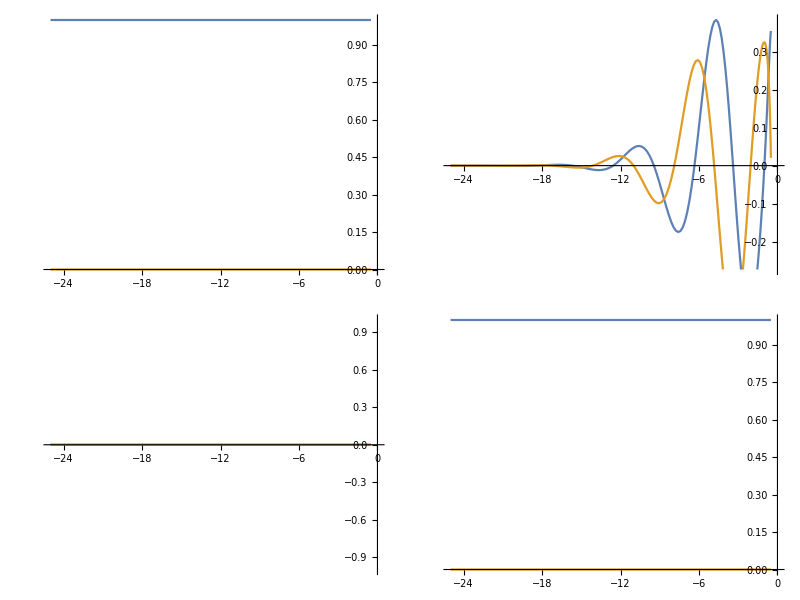
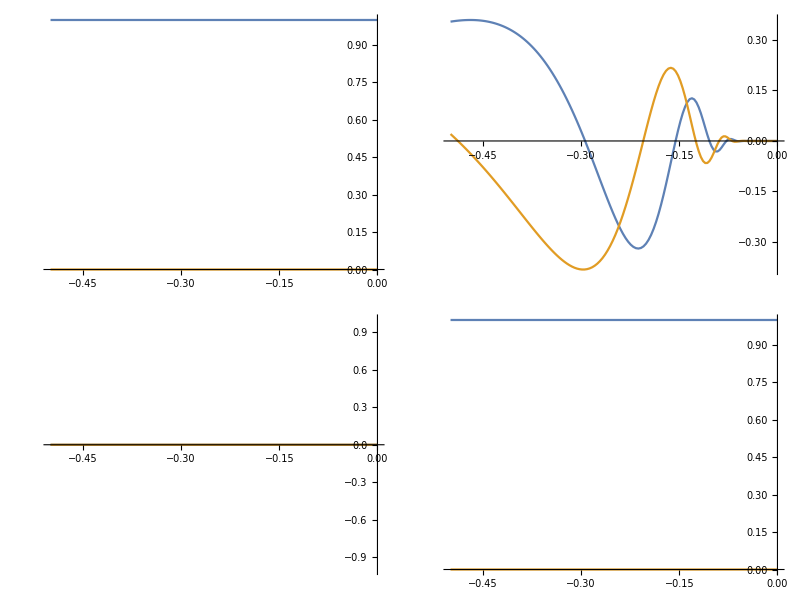
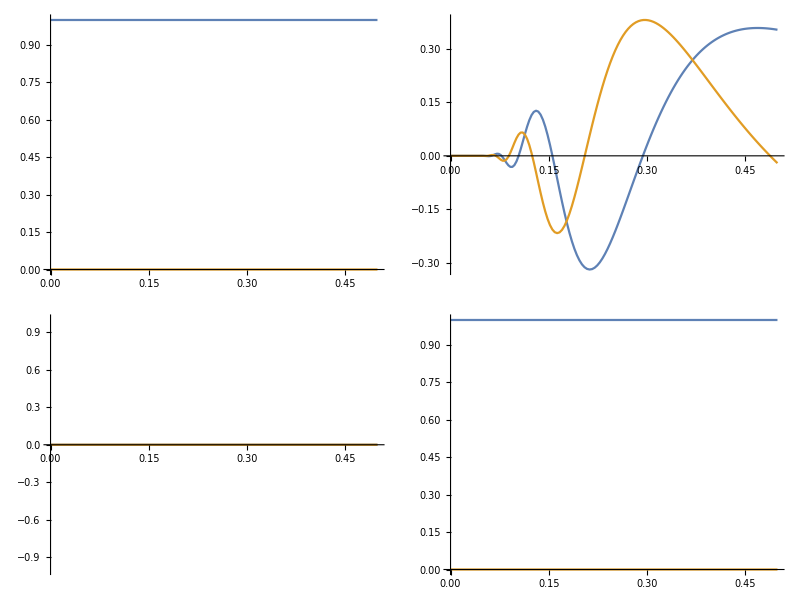
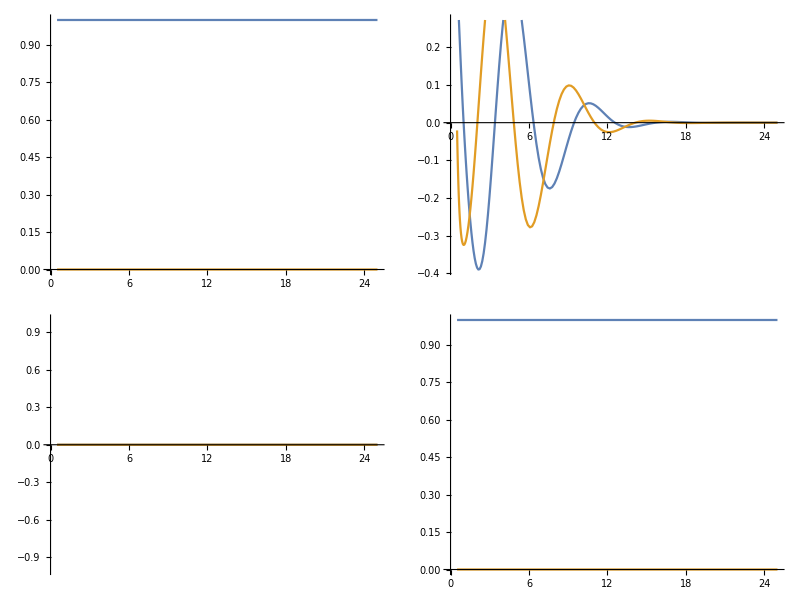
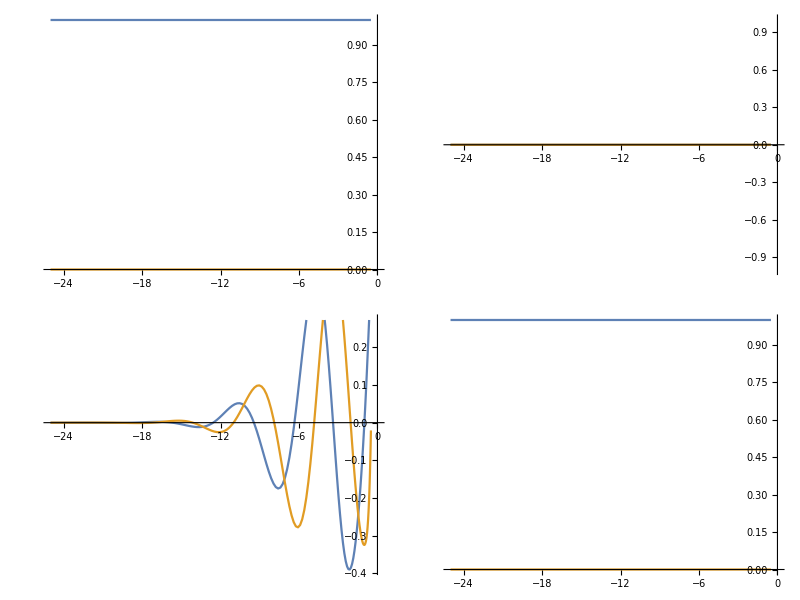
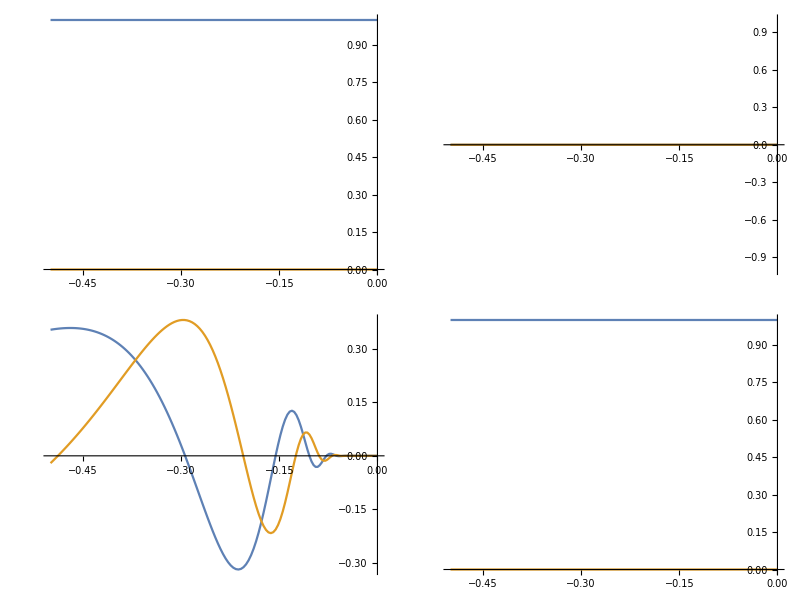
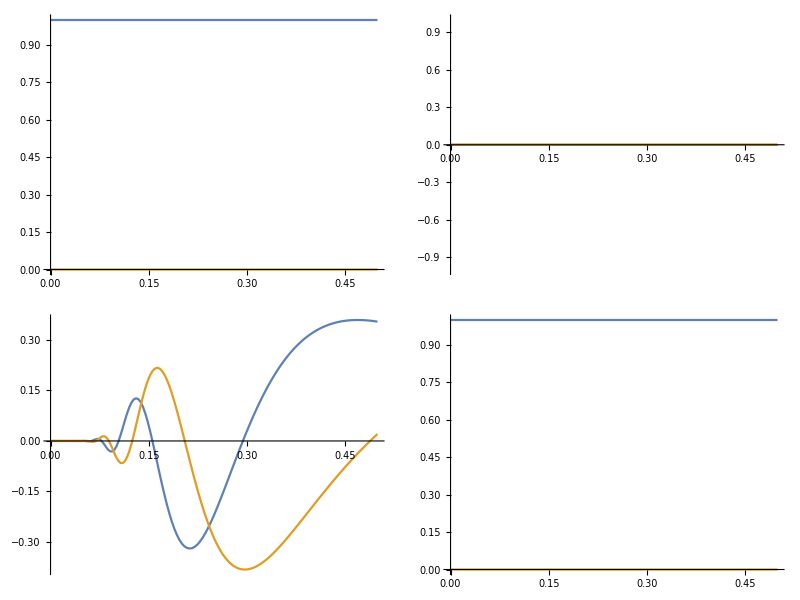
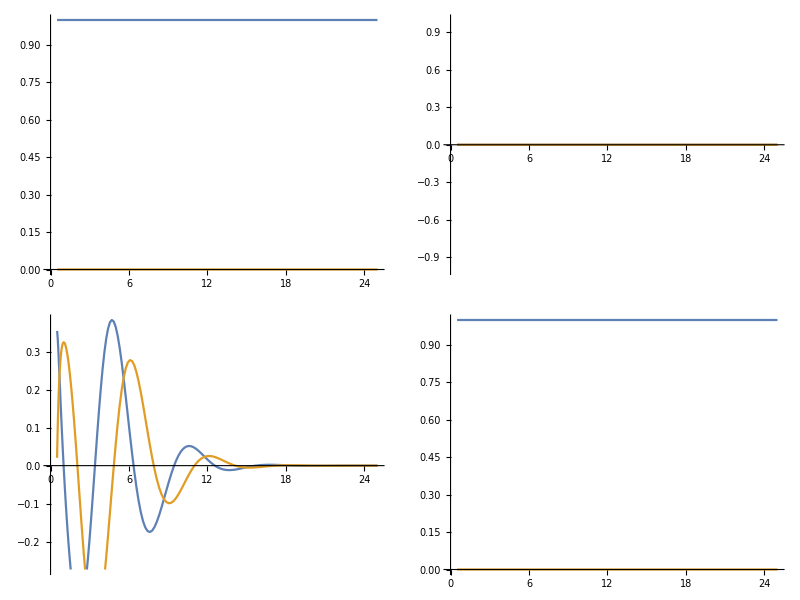
{(-Graphics-),(-Graphics-),(-Graphics-),(-Graphics-),(-Graphics-),(-Graphics-),(-Graphics-),(-Graphics-)}

```mathematica
Grhp1
```

```mathematica
mRHWellPosed[Grhp1]
```

((1. | -4.3461×10^-8-7.40254×10^-8 ⅈ
0 | 1.) | -37.0625-0.02 ⅈ
(1. | 0
-4.3461×10^-8+7.40254×10^-8 ⅈ | 1.) | -37.0625+0.02 ⅈ
(1. | 0
0 | 1.) | -0.4996-0.02 ⅈ
(1. | 0
0 | 1.) | -0.4996+0.02 ⅈ
(1. | 0.000252352-0.000467253 ⅈ
0 | 1.) | -0.11241-0.0045 ⅈ
(1. | 0
0.000252352+0.000467253 ⅈ | 1.) | -0.11241+0.0045 ⅈ
(1. | -0.000252352-0.000467253 ⅈ
0 | 1.) | 0.11241-0.0045 ⅈ
(1. | 0
-0.000252352+0.000467253 ⅈ | 1.) | 0.11241+0.0045 ⅈ
(1. | 0
0 | 1.) | 0.4996-0.02 ⅈ
(1. | 0
0 | 1.) | 0.4996+0.02 ⅈ
(1. | 4.39139×10^-8-7.37782×10^-8 ⅈ
0 | 1.) | 37.0621-0.02 ⅈ
(1. | 0
4.39139×10^-8+7.37782×10^-8 ⅈ | 1.) | 37.0621+0.02 ⅈ)

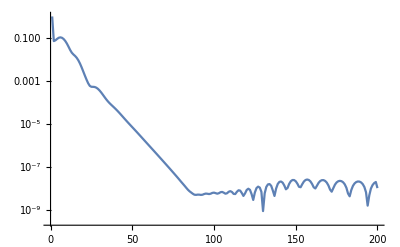
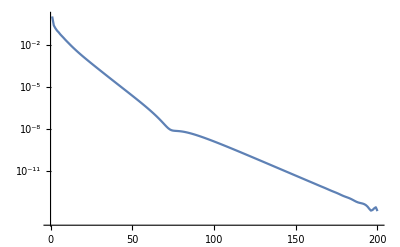
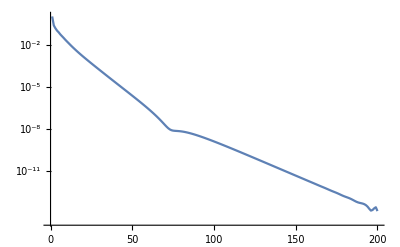
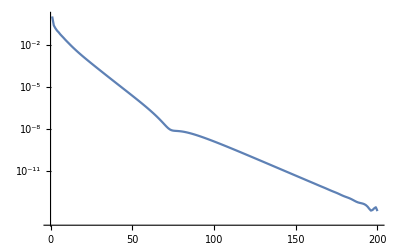
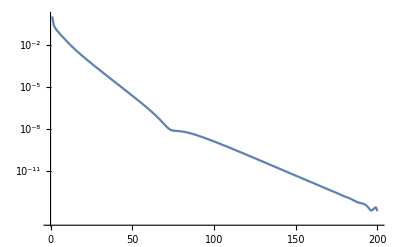
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
DCTPlot/@ Grhp1
```

```mathematica
nu1=Sqrt[1/(8ν)^2-(1/(8ν)-ν)^2];
Clear[x];
Clear[t];
x=-4;t=2;
bigN=200;
r1=Fun[Φt[x,t][#].L[x,t][#].Φtin[x,t][#]&,Line[{-el-I*ν,-nu1-I*ν}],bigN];
r2=Fun[L[x,t][#]&,Line[{-el-I*ν,-nu1-I*ν}],bigN];
r3=Fun[Φt[x,t][#]&,Line[{-el-I*ν,-nu1-I*ν}],bigN];
```

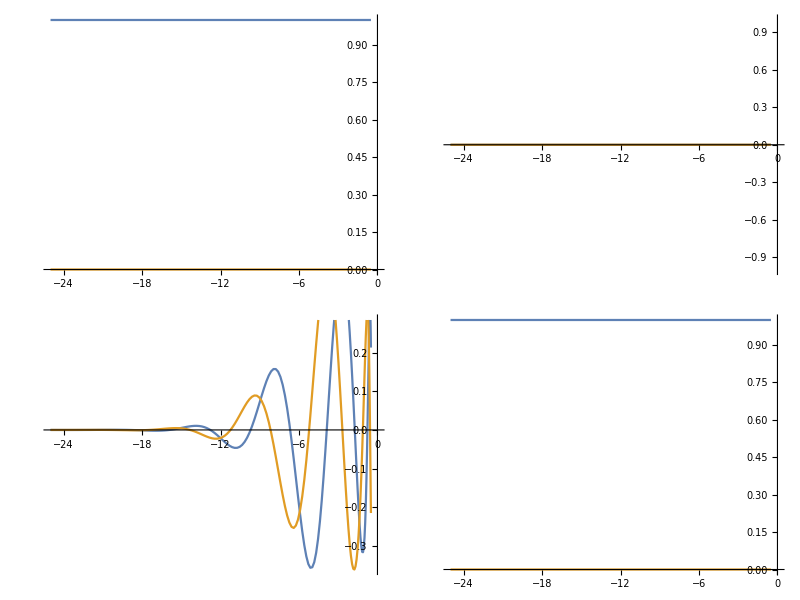
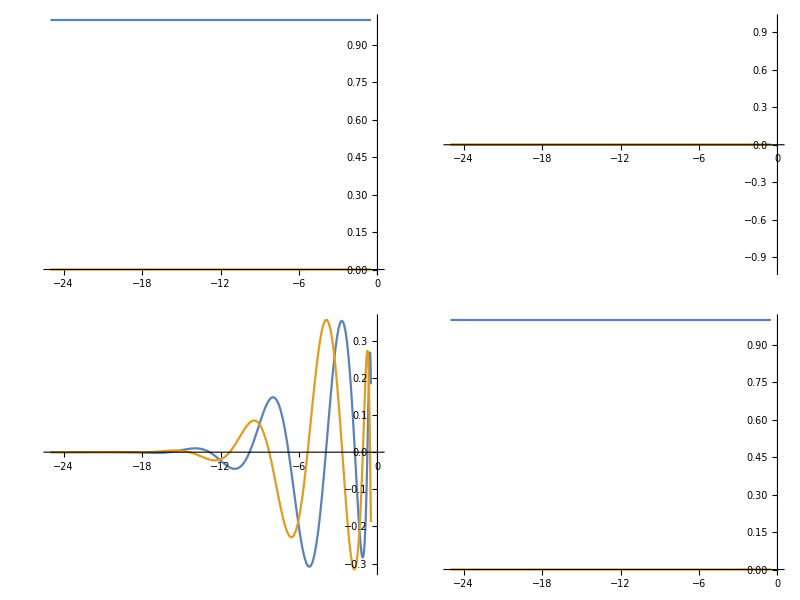
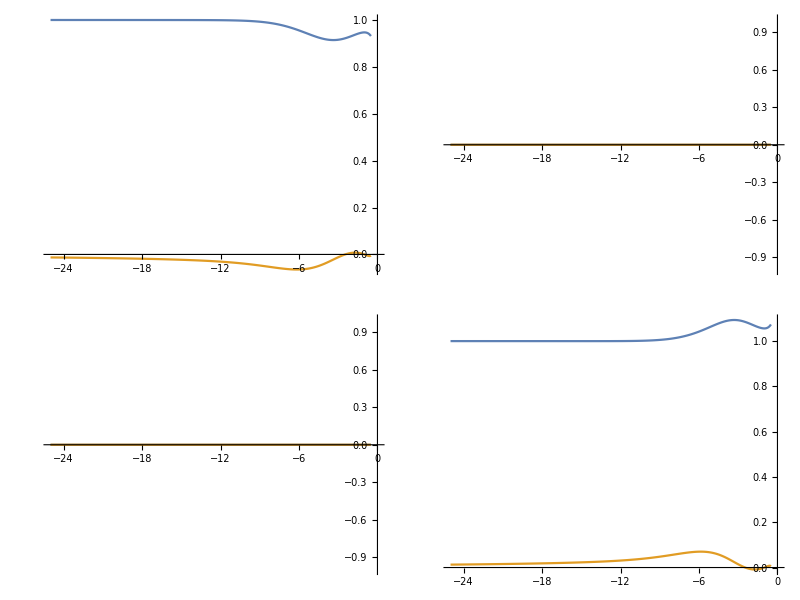
{(-Graphics-),(-Graphics-),(-Graphics-)}

```mathematica
{r1,r2,r3}
```

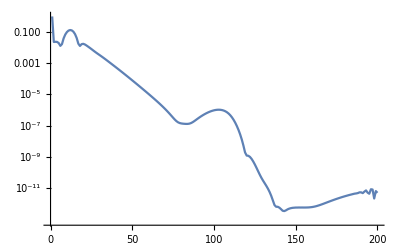
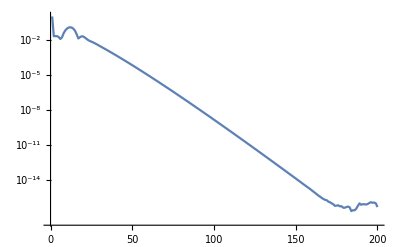
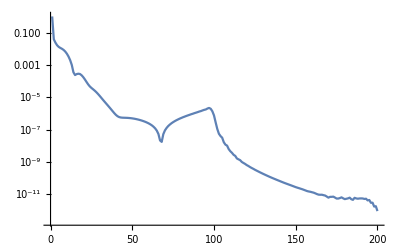

```mathematica
DCTPlot/@{r1,r2,r3}
```

```mathematica
(*why there's a bump near 100?*)
```

```mathematica
nu1=Sqrt[1/(8ν)^2-(1/(8ν)-ν)^2];
τ[k_]:=1+ ρ[k]cc[ρ[cc[k]]];
bigN=200;
ift=Fun[Log[τ[#]]&,{-el,0}//Line,bigN];
iftb=Fun[Log[τ[#]]&,{0,el}//Line,bigN];
deltat[k_]:=Exp[(Cauchy[ift,k]+Cauchy[iftb,k])];
```

```mathematica
r4=Fun[deltat[#]&,Line[{-el-I*ν,-nu1-I*ν}],bigN];
iftc=Fun[Log[τ[#]]&,{-el,el}//Line,bigN];
r5=Fun[Exp[Cauchy[iftc,#]]&,Line[{-el-I*ν,-nu1-I*ν}],bigN];
```

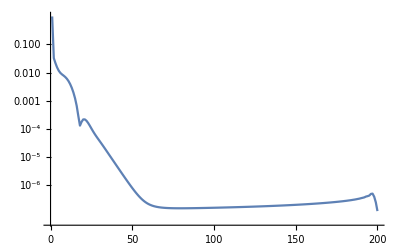
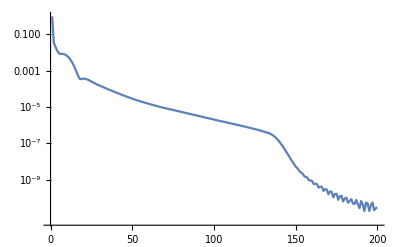

```mathematica
DCTPlot/@{r4,r5}
```

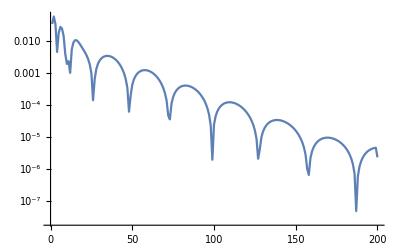

```mathematica
DCTPlot[ift]
```

```mathematica
(*use a simple rho*)
nu1=Sqrt[1/(8ν)^2-(1/(8ν)-ν)^2];
ρ1[k_]:=k^2/(1+k^4);
τ1[k_]:=1+ ρ1[k]cc[ρ1[cc[k]]];
bigN=200;
ift=Fun[Log[τ1[#]]&,{-el,0}//Line,bigN];
iftb=Fun[Log[τ1[#]]&,{0,el}//Line,bigN];
deltat[k_]:=Exp[(Cauchy[ift,k]+Cauchy[iftb,k])];
r4=Fun[deltat[#]&,Line[{-el-I*ν,-nu1-I*ν}],bigN];
iftc=Fun[Log[τ1[#]]&,{-el,el}//Line,bigN];
r5=Fun[Exp[Cauchy[iftc,#]]&,Line[{-el-I*ν,-nu1-I*ν}],bigN];
```

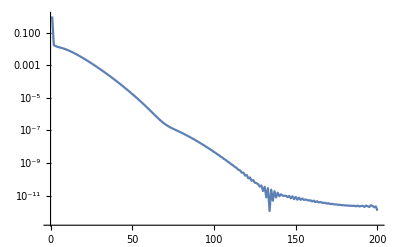
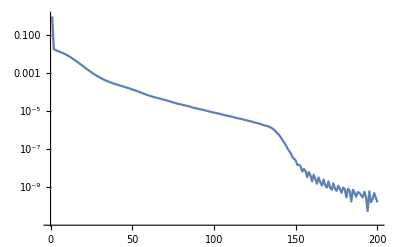

```mathematica
DCTPlot/@{r4,r5}
```

```mathematica
{out,phi,rhp1,rhp2,ttime}=SG[2][-0.2,0];
```

```mathematica
qSG[-0.2,0]
```

{{0.721557+0.0128277 ⅈ,0.819056-0.0377334 ⅈ},{0.585254+0.00436086 ⅈ,-0.721557-0.0128277 ⅈ}}

```mathematica
qSG[0.2,0]
```

{{0.721557-0.0128277 ⅈ,0.819056+0.0377334 ⅈ},{0.585254-0.00436086 ⅈ,-0.721557+0.0128277 ⅈ}}

```mathematica
out
```

{{0.863762+0.0253372 ⅈ,0.568335-0.105698 ⅈ},{0.446769+0.00607366 ⅈ,-0.863762-0.0253372 ⅈ}}

```mathematica
phi[0].{{1,0},{0,-1}}.Inverse[phi[0]]
```

{{0.863762+0.0253372 ⅈ,0.568335-0.105698 ⅈ},{0.446769+0.00607366 ⅈ,-0.863762-0.0253372 ⅈ}}

```mathematica
phi[0+0.000001I]-phi[0-0.000001I]
phi[0+0.000001I]-phi[0]
```

{{9.42509×10^-8-4.40159×10^-12 ⅈ,-7.67596×10^-7-8.52927×10^-12 ⅈ},{-7.67596×10^-7+8.52935×10^-12 ⅈ,-9.42509×10^-8-4.40157×10^-12 ⅈ}}

{{4.71263×10^-8-2.15249×10^-12 ⅈ,-0.0393441-0.0372967 ⅈ},{0.141215+4.13036×10^-12 ⅈ,0.0393436+0.0326001 ⅈ}}

```mathematica
Cauchy[RHSolve[MakeListFun[J[0][xx,tt]]],2+I]+IdentityMatrix[2]
```

{{1.02666-0.0157937 ⅈ,-0.106397-0.0671987 ⅈ},{-0.00442163+0.208449 ⅈ,0.988226-0.00611047 ⅈ}}

```mathematica
P[xx,tt][(-1+I)/2](*not well posed in the lower half plane*)
```

{{1,0},{0.302373+0.0379947 ⅈ,1}}

```mathematica
M[xx,tt][(-1-I)/2].P[xx,tt][(-1-I)/2]-G[xx,tt][(-1-I)/2]
```

{{0.+2.77556×10^-17 ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ}}

```mathematica
H[-1.61I]
```

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«150»},«49»,«150»} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {«1»} may contain significant numerical errors.

General::stop: Further output of LinearSolve::luc will be suppressed during this calculation.

{{1.26732,-0.414477},{0.414477,-0.924624}}

```mathematica
tt=0;
G[xx,tt][10]
```

{{1.00023+0. ⅈ,-0.00908565+0.0123402 ⅈ},{-0.00908565-0.0123402 ⅈ,1}}

```mathematica
{out,phi,rhp1,rhp2,tt}=SG[0][0.5,0];
```

```mathematica
phi[I+0.000000001I]-phi[I-0.000000001I]
```

{{1.98304×10^-9+1.21431×10^-17 ⅈ,8.34418×10^-11-2.25514×10^-17 ⅈ},{-1.3731×10^-8+1.38778×10^-17 ⅈ,7.40041×10^-12-8.67362×10^-19 ⅈ}}

```mathematica
phi[I-0.00001]
```

{{0.97181+5.63957×10^-7 ⅈ,-0.141+4.17211×10^-7 ⅈ},{0.300914-3.30574×10^-6 ⅈ,0.985348+3.70024×10^-8 ⅈ}}

```mathematica
θ[x_,t_][z_]:= Piecewise[{{0,z==0},{2*I/4 ((z+1/z)t+(z-1/z)x ),z≠0}}];    
exppt[x_,t_][z_]:=Piecewise[{{0,z==0},{Exp[θ[x,t][z]],z≠0}}];
P[x_,t_][k_]:=({{1, 0}, {ρ[k] exppt[x,t][k], 1}});
```

```mathematica
P[0.5,0][I]
```

{{1,0},{-1.37507×10^-8+0. ⅈ,1}}

```mathematica
ρ[1.3I]
```

-0.220326

```mathematica
Grhp1[[1]][[1,2]][-0.6]
```

0.232512-0.486601 ⅈ

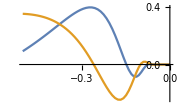

```mathematica
Grhp1[[2]][[1,2]]
```

```mathematica
ss=0.00001;
M[2,1][ss][[1,2]]
ρ[ss]
```

1.18013×10^-17+3.82082×10^-19 ⅈ

-5.93172×10^-19-1.17926×10^-17 ⅈ

General::stop: Further output of LinearSolve::luc will be suppressed during this calculation.

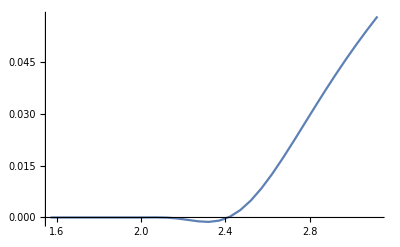

```mathematica
TablePlot[Re[M[2,1][-0.1I+0.1*Exp[I*s]][[1,2]]],{s,π/2,π,0.1/2}]
```

```mathematica
Re[M[2,1][-0.1I+0.1*Exp[I*(π/2+0.24)]][[1,2]]]
```

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{0.999716+0.0023547 ⅈ,0.000568508-0.0047094 ⅈ,-0.000568508+0.0047094 ⅈ,0.000568508-0.0047094 ⅈ,-0.000568508+0.0047094 ⅈ,0.000568508-0.0047094 ⅈ,-0.000568508+0.0047094 ⅈ,0.000568508-0.0047094 ⅈ,«36»,-0.000568508+0.0047094 ⅈ,0.000568508-0.0047094 ⅈ,-0.000568508+0.0047094 ⅈ,0.000568508-0.0047094 ⅈ,-0.000568508+0.0047094 ⅈ,0.000568508-0.0047094 ⅈ,«150»},{«1»},«47»,{-«22»+«21» ⅈ,«49»,«150»},«150»} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{1.-9.43833×10^-7 ⅈ,-1.53193×10^-6-0.0000127047 ⅈ,-2.91994×10^-6-0.0000242159 ⅈ,-4.5331×10^-6-0.0000375944 ⅈ,-5.85517×10^-6-0.0000485586 ⅈ,-7.41728×10^-6-0.0000615137 ⅈ,-8.61752×10^-6-0.0000714676 ⅈ,-9.97967×10^-6-0.0000827644 ⅈ,-0.0000108784-0.0000902175 ⅈ,«34»,-4.71353×10^-15-3.90907×10^-14 ⅈ,-1.54208×10^-15-1.27889×10^-14 ⅈ,-5.03878×10^-16-4.17881×10^-15 ⅈ,0.-1.34793×10^-15 ⅈ,0.-4.35341×10^-16 ⅈ,0.+0. ⅈ,0.+0. ⅈ,«150»},{«1»},«47»,{«1»},«150»} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{0.999716+0.0023547 ⅈ,0.000568508-0.0047094 ⅈ,-0.000568508+0.0047094 ⅈ,0.000568508-0.0047094 ⅈ,-0.000568508+0.0047094 ⅈ,0.000568508-0.0047094 ⅈ,-0.000568508+0.0047094 ⅈ,0.000568508-0.0047094 ⅈ,«36»,-0.000568508+0.0047094 ⅈ,0.000568508-0.0047094 ⅈ,-0.000568508+0.0047094 ⅈ,0.000568508-0.0047094 ⅈ,-0.000568508+0.0047094 ⅈ,0.000568508-0.0047094 ⅈ,«150»},{«1»},«47»,{-«22»+«21» ⅈ,«49»,«150»},«150»} may contain significant numerical errors.

General::stop: Further output of LinearSolve::luc will be suppressed during this calculation.

-6.49773×10^-11

```mathematica
Re[M[2,1][-0.1I+0.1*Exp[I*(π/2+1.94)]][[1,2]]]
```

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{0.999708+0.00018939 ⅈ,0.000583646-0.000378781 ⅈ,-0.000583646+0.000378781 ⅈ,0.000583646-0.000378781 ⅈ,-0.000583646+0.000378781 ⅈ,0.000583646-0.000378781 ⅈ,-0.000583646+0.000378781 ⅈ,0.000583646-0.000378781 ⅈ,«36»,-0.000583646+0.000378781 ⅈ,0.000583646-0.000378781 ⅈ,-0.000583646+0.000378781 ⅈ,0.000583646-0.000378781 ⅈ,-0.000583646+0.000378781 ⅈ,0.000583646-0.000378781 ⅈ,«150»},{«1»},«47»,{«1»},«150»} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{0.999995-3.70308×10^-6 ⅈ,-0.000072736-0.0000498465 ⅈ,-0.000138639-0.0000950101 ⅈ,-0.000215232-0.0001475 ⅈ,-0.000278003-0.000190518 ⅈ,-0.000352172-0.000241346 ⅈ,-0.00040916-0.0002804 ⅈ,-0.000473835-0.000324722 ⅈ,«36»,-7.32181×10^-14-5.01768×10^-14 ⅈ,-2.39241×10^-14-1.63953×10^-14 ⅈ,-7.71703×10^-15-5.28853×10^-15 ⅈ,-2.49237×10^-15-1.70804×10^-15 ⅈ,-7.96646×10^-16-5.45947×10^-16 ⅈ,-2.55501×10^-16+0. ⅈ,«150»},{«1»},«47»,{«1»},«150»} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{0.999708+0.00018939 ⅈ,0.000583646-0.000378781 ⅈ,-0.000583646+0.000378781 ⅈ,0.000583646-0.000378781 ⅈ,-0.000583646+0.000378781 ⅈ,0.000583646-0.000378781 ⅈ,-0.000583646+0.000378781 ⅈ,0.000583646-0.000378781 ⅈ,«36»,-0.000583646+0.000378781 ⅈ,0.000583646-0.000378781 ⅈ,-0.000583646+0.000378781 ⅈ,0.000583646-0.000378781 ⅈ,-0.000583646+0.000378781 ⅈ,0.000583646-0.000378781 ⅈ,«150»},{«1»},«47»,{«1»},«150»} may contain significant numerical errors.

General::stop: Further output of LinearSolve::luc will be suppressed during this calculation.

0.0862247

```mathematica
Re[M[2,1][-0.1I-0.1+0.000001][[1,2]]]
```

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{0.99971+0.000278409 ⅈ,0.000579551-0.000556818 ⅈ,-0.000579551+0.000556818 ⅈ,0.000579551-0.000556818 ⅈ,-0.000579551+0.000556818 ⅈ,0.000579551-0.000556818 ⅈ,-0.000579551+0.000556818 ⅈ,0.000579551-0.000556818 ⅈ,«36»,-0.000579551+0.000556818 ⅈ,0.000579551-0.000556818 ⅈ,-0.000579551+0.000556818 ⅈ,0.000579551-0.000556818 ⅈ,-0.000579551+0.000556818 ⅈ,0.000579551-0.000556818 ⅈ,«150»},{-«22»+«21» ⅈ,«50»},«48»,«150»} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{0.999996-3.9706×10^-6 ⅈ,-0.0000534481-0.0000534475 ⅈ,-0.000101875-0.000101874 ⅈ,-0.000158157-0.000158156 ⅈ,-0.000204283-0.000204281 ⅈ,-0.000258784-0.000258782 ⅈ,-0.00030066-0.000300657 ⅈ,-0.000348184-0.000348181 ⅈ,«36»,-5.38023×10^-14-5.38017×10^-14 ⅈ,-1.758×10^-14-1.75798×10^-14 ⅈ,-5.67064×10^-15-5.67059×10^-15 ⅈ,-1.83145×10^-15-1.83143×10^-15 ⅈ,-5.85393×10^-16-5.85388×10^-16 ⅈ,0.+0. ⅈ,«150»},«49»,«150»} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{0.99971+0.000278409 ⅈ,0.000579551-0.000556818 ⅈ,-0.000579551+0.000556818 ⅈ,0.000579551-0.000556818 ⅈ,-0.000579551+0.000556818 ⅈ,0.000579551-0.000556818 ⅈ,-0.000579551+0.000556818 ⅈ,0.000579551-0.000556818 ⅈ,«36»,-0.000579551+0.000556818 ⅈ,0.000579551-0.000556818 ⅈ,-0.000579551+0.000556818 ⅈ,0.000579551-0.000556818 ⅈ,-0.000579551+0.000556818 ⅈ,0.000579551-0.000556818 ⅈ,«150»},{-«22»+«21» ⅈ,«50»},«48»,«150»} may contain significant numerical errors.

General::stop: Further output of LinearSolve::luc will be suppressed during this calculation.

0.0597813

```mathematica
DCTPlot/@ Grhp2
```

Grhp2

```mathematica
mRHWellPosed[Grhp1]
```

((1. | 2.96612×10^-6+8.295×10^-7 ⅈ
0 | 1.) | -30.-0.02 ⅈ
(1. | 0
2.96612×10^-6-8.295×10^-7 ⅈ | 1.) | -30.+0.02 ⅈ
(1. | 0
0 | 1.) | -0.4996-0.02 ⅈ
(1. | 0
0 | 1.) | -0.4996+0.02 ⅈ
(1 | 0
0 | 1) | 0
(1. | 0
0 | 1.) | 0.4996-0.02 ⅈ
(1. | 0
0 | 1.) | 0.4996+0.02 ⅈ
(1. | -2.96612×10^-6+8.295×10^-7 ⅈ
0 | 1.) | 30.-0.02 ⅈ
(1. | 0
-2.96612×10^-6-8.295×10^-7 ⅈ | 1.) | 30.+0.02 ⅈ)

```mathematica
θ[x_,t_][z_]:= Piecewise[{{0,z==0},{2*I/4 ((z+1/z)t+(z-1/z)x ),z≠0}}];
```

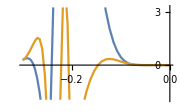

```mathematica
r1=Fun[cc[ρ[cc[#]]]*Exp[-θ[1,0][#]]&,Line[{-ν-I*ν,-(1+I)*0.001}],60]
```

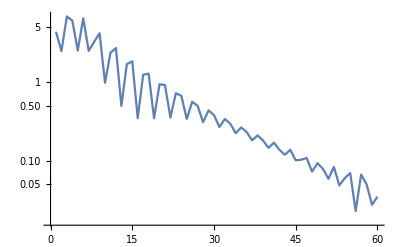

```mathematica
DCTPlot[r1]
```

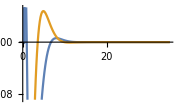

Thread::tdlen: Objects of unequal length in {«1»}+{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,«50»} cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

Diagonal::list: List expected at position 1 in ….

General::stop: Further output of Diagonal::list will be suppressed during this calculation.

$Aborted

$Aborted

```mathematica
r4=Fun[cc[ρ[cc[#]]]*Exp[-θ[1,0][#]]&,Line[{-I*ν,35-I*ν}],200]
```

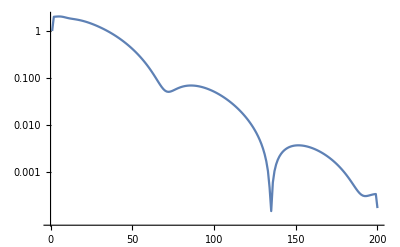

```mathematica
DCTPlot[r4]
```

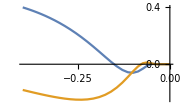

```mathematica
tt1=Fun[Exp[-θ[1,0][#]]&,Line[{-ν-I*ν,(-1-I)*0.0001}],40]
```

```mathematica
θ[1,0][0.00001*Exp[I Pi*3/2]]
```

50000.+0. ⅈ

```mathematica
θ[1,0][-0.00001]
```

0.+50000. ⅈ

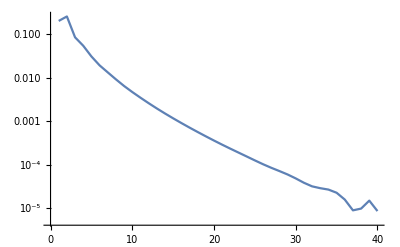

```mathematica
DCTPlot[tt1]
```

```mathematica
DCTPlot[Fun[Exp[-θ[1,0][#]]&,Line[{-ν-I*ν,0}],100]]
```

$Aborted

$Aborted

```mathematica
myacos[ans]
q[xx]
```

4.53638

4.53638

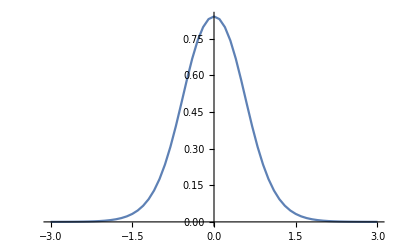

```mathematica
TablePlot[Sin[q[x]],{x,-3,3,0.1},PlotRange->All]
```

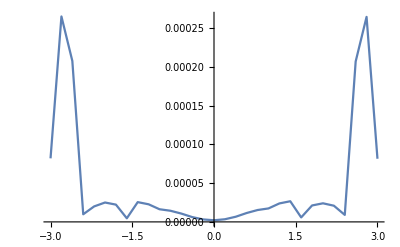

```mathematica
Monitor[TablePlot[Abs[qSG[x,0][[1,2]]-Sin[q[x]]],{x,-3.,3,0.2},PlotRange->All],timestring]
```

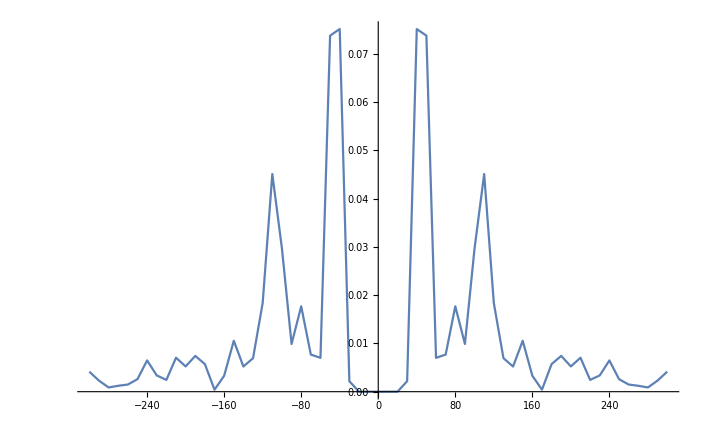

```mathematica
TablePlot[Abs[qSG[x,0][[1,2]]-Sin[q[x]]],{x,-300.,300,10},PlotRange->All]
```

```mathematica
q[8.]
```

2.02627×10^-13

```mathematica
qSG[40,0][[1,2]]
```

0.0751597+0.0000289897 ⅈ

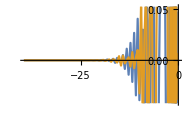

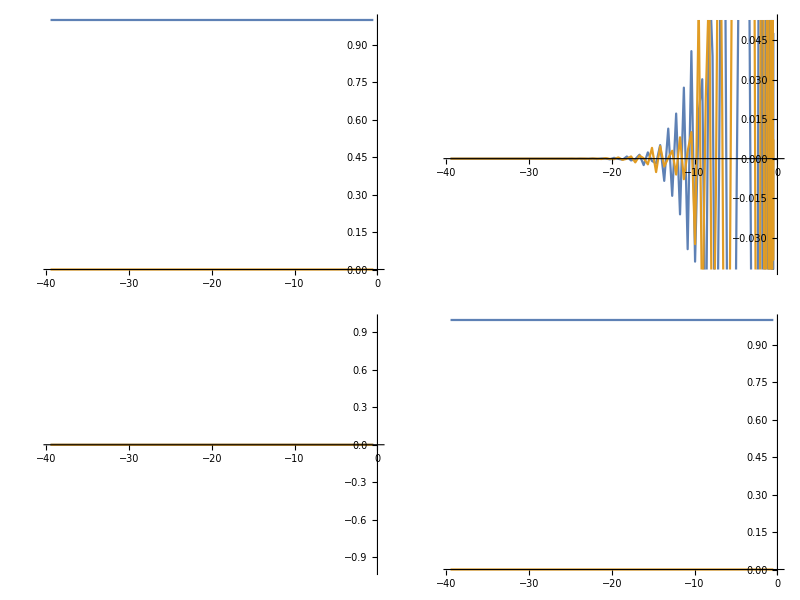
(-Graphics-)

```mathematica
Grhp1[[1]][[1,2]]
```

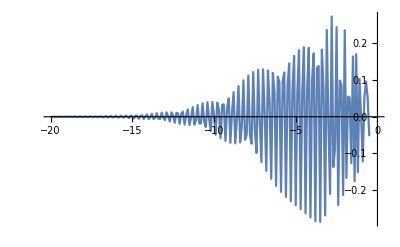

```mathematica
TablePlot[Re[M[40,0][k-I (ν)][[1,2]]],{k,-20,-nu1,0.1}]
```

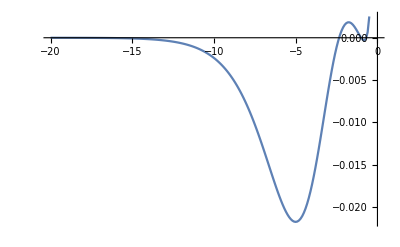

```mathematica
TablePlot[Re[ρ[cc[k-I (ν)]]],{k,-20,-nu1,0.1}]
```

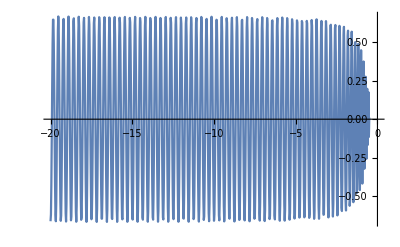

```mathematica
θ[x_,t_][z_]:= Piecewise[{{0,z==0},{2*I/4 ((z+1/z)t+(z-1/z)x ),z≠0}}]; 
TablePlot[Re[Exp[-θ[40,0.01][k-I (ν)]]],{k,-20,-nu1,0.1/4}]
```

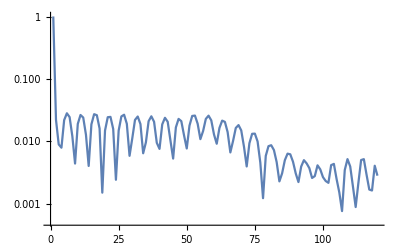
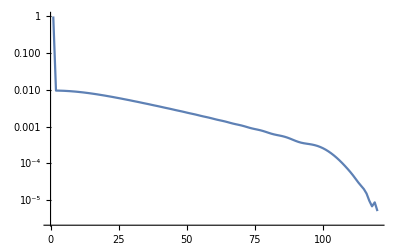
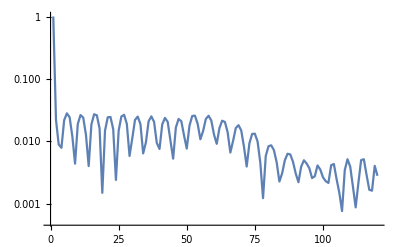
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
DCTPlot/@ Grhp1
```

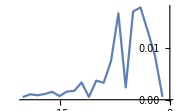

```mathematica
TablePlot[Abs[Grhp1[[1]][[1,2]][x]],{x,-20,-0.5,1}]
```

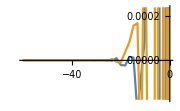

{1.45254×10^-10,1.47546×10^-10,1.54636×10^-10,1.67203×10^-10,1.86493×10^-10,2.14525×10^-10,2.54434×10^-10,3.1104×10^-10,3.91774×10^-10,5.08206×10^-10,6.78597×10^-10,9.3219×10^-10,1.31657×10^-9,1.91043×10^-9,2.84598×10^-9,4.34895×10^-9,6.81079×10^-9,1.09205×10^-8,1.79087×10^-8,3.00027×10^-8,5.12859×10^-8,8.9331×10^-8,1.58325×10^-7,2.85084×10^-7,5.20652×10^-7,9.62702×10^-7,1.7987×10^-6,3.38865×10^-6,6.42228×10^-6,0.0000122135,0.0000232415,0.0000441169,0.0000832443,0.000155527,0.000286434,0.000517342,0.000910915,0.00155265,0.00254053,0.00395018,0.00576386,0.00776965,0.00948373,0.0102127,0.00937525,0.00701312,0.00404857,0.00174598,0.000653526,0.000394911}

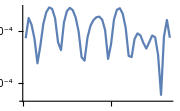

```mathematica
nu1=Sqrt[1/(8ν)^2-(1/(8ν)-ν)^2];
ff1=Fun[Msamp[30,0][#][[1,2]]&,Line[{-el-I*ν,-nu1-I*ν}],50]
Abs[Values[ff1]]
DCTPlot[ff1]
```

```mathematica
qSG[2000,0]
```

{{1.+4.10439×10^-37 ⅈ,-4.23416×10^-11+2.64233×10^-22 ⅈ},{-4.23416×10^-11-2.64213×10^-22 ⅈ,-1.-4.10439×10^-37 ⅈ}}

```mathematica
ρ[25+20I]
```

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{0.99599+0.00500313 ⅈ,0.00802064-0.0100063 ⅈ,-0.00802064+0.0100063 ⅈ,0.00802064-0.0100063 ⅈ,«44»,1.95241×10^-10-1.19665×10^-12 ⅈ,-3.2485×10^-10+1.99113×10^-12 ⅈ,«30»},{«1»},«47»,{«1»},«30»} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{0.999997-3.48421×10^-6 ⅈ,-0.0000372659-0.0000465823 ⅈ,-0.0000706717-0.0000883397 ⅈ,-0.000107622-0.000134528 ⅈ,«44»,0.034684+0.000423967 ⅈ,0.0358898+0.000374975 ⅈ,«30»},{«1»},«47»,{«1»},«30»} may contain significant numerical errors.

-0.251664-0.566433 ⅈ

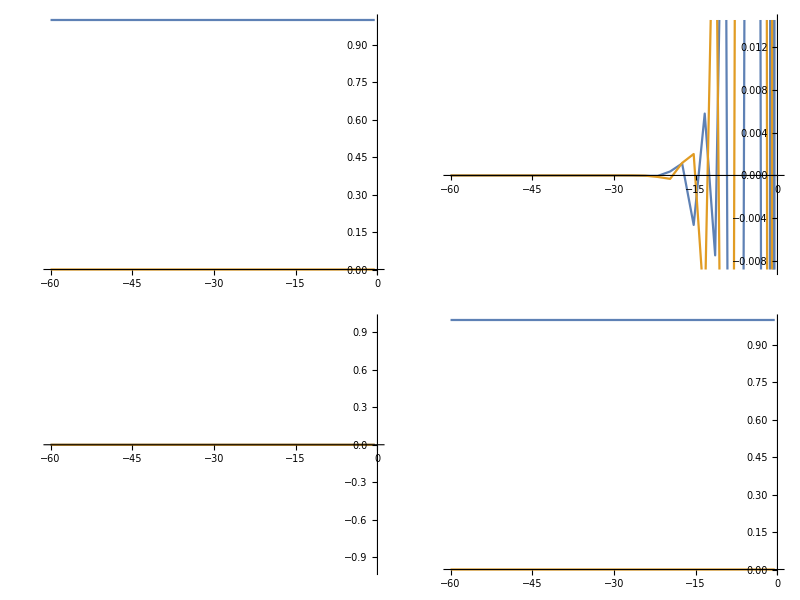
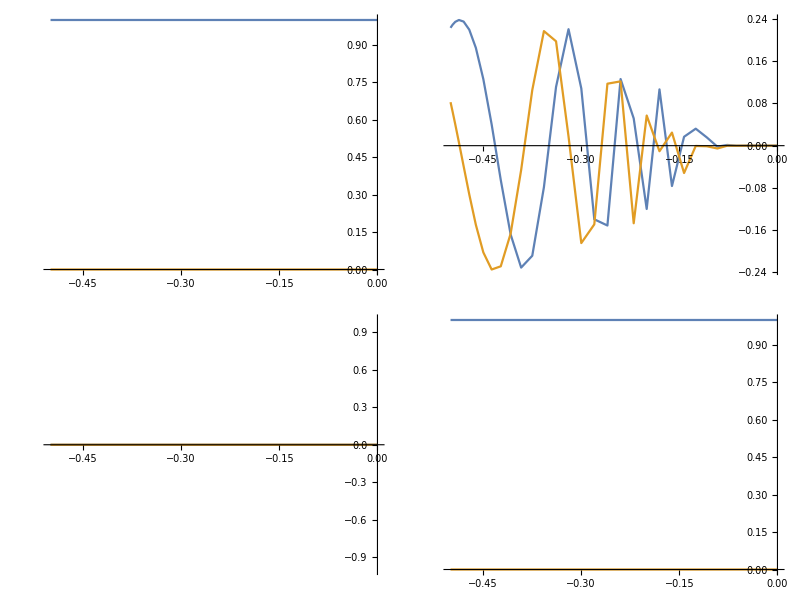
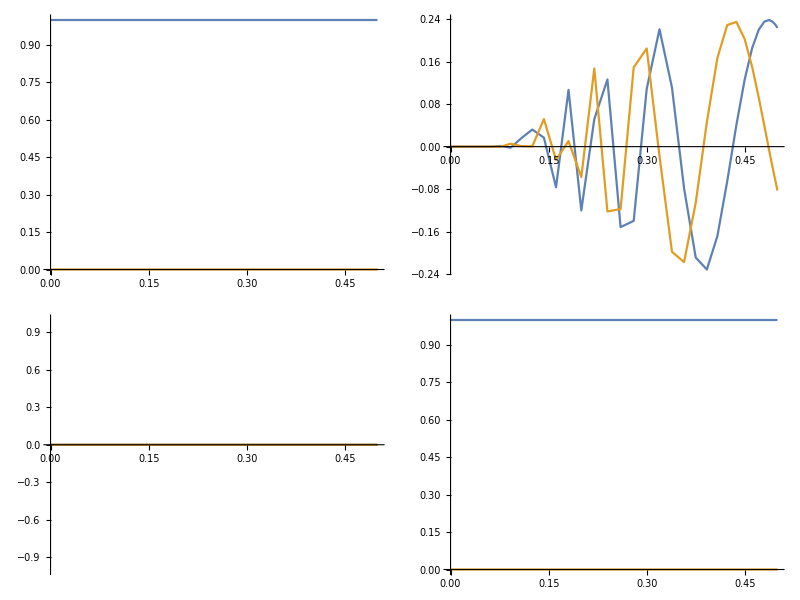
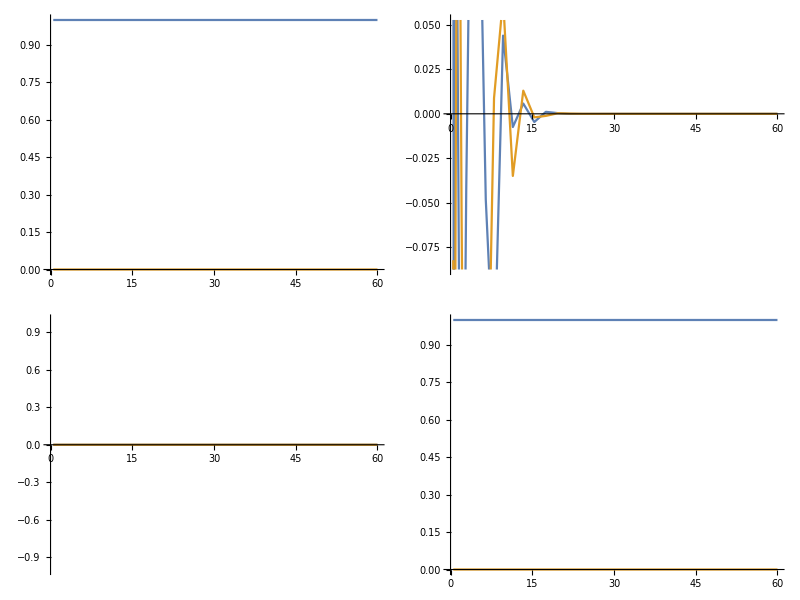
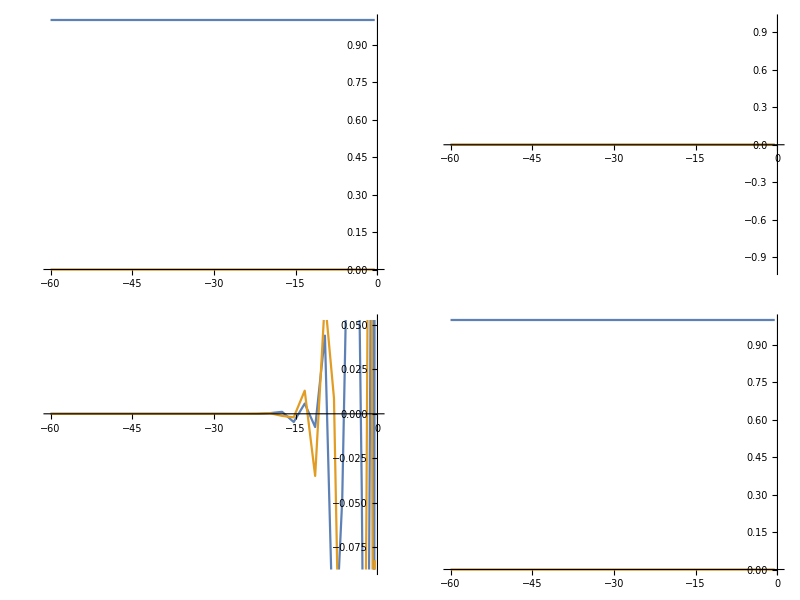
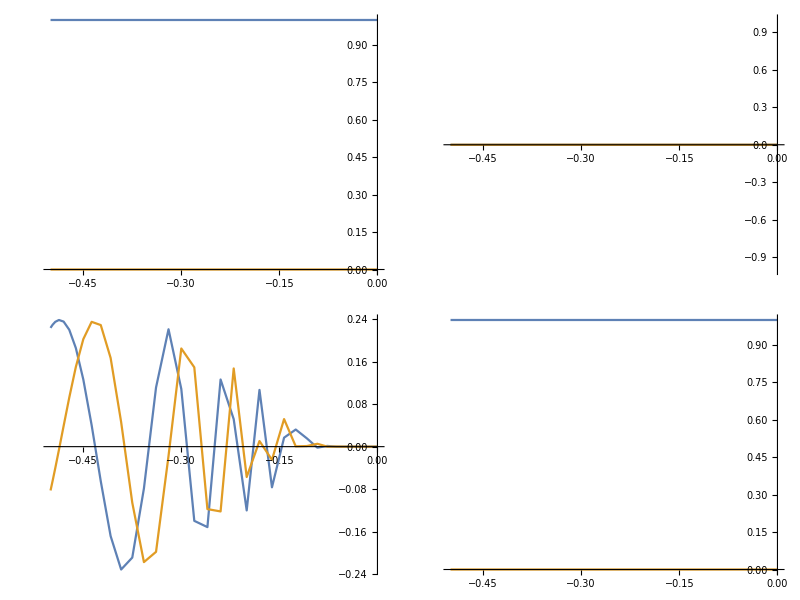
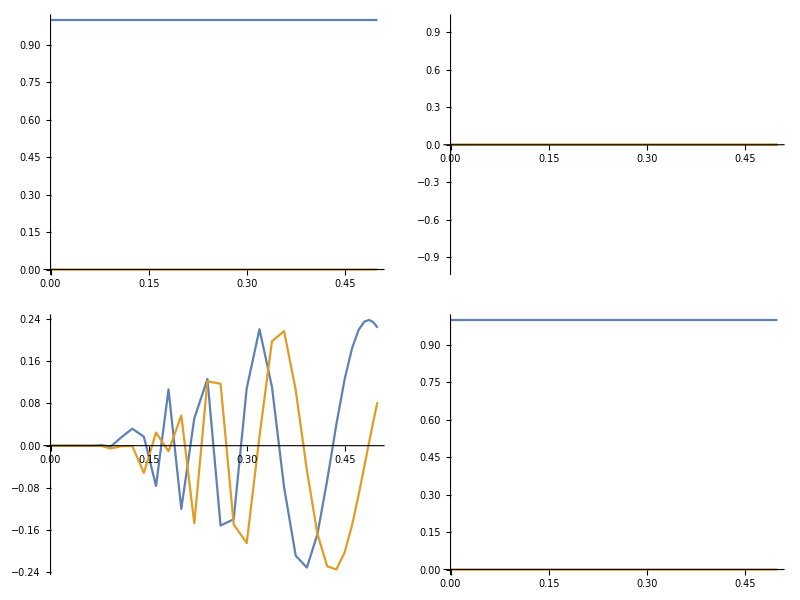
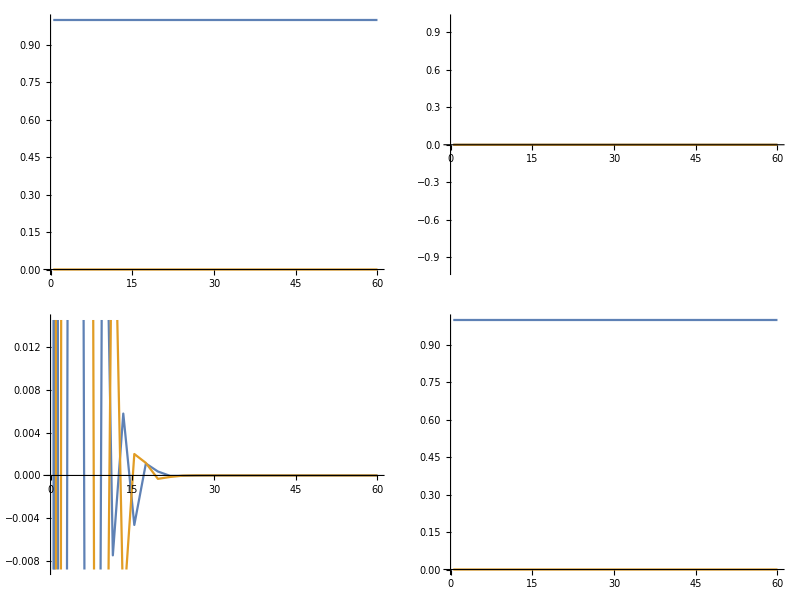
{(-Graphics-),(-Graphics-),(-Graphics-),(-Graphics-),(-Graphics-),(-Graphics-),(-Graphics-),(-Graphics-)}

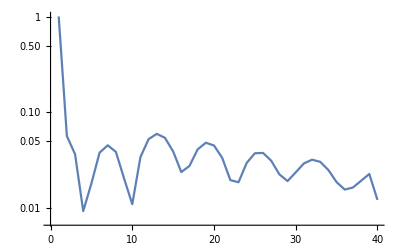
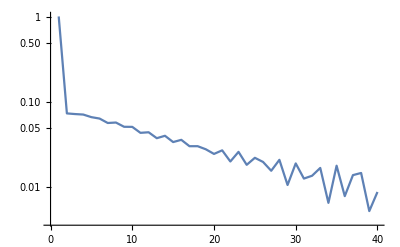
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Grhp1
DCTPlot/@Grhp1
```

```mathematica
qSG[50,0]
```

{{0.99993-1.02638×10^-19 ⅈ,0.011806+5.17239×10^-15 ⅈ},{0.011806-5.15501×10^-15 ⅈ,-0.99993+1.02638×10^-19 ⅈ}}

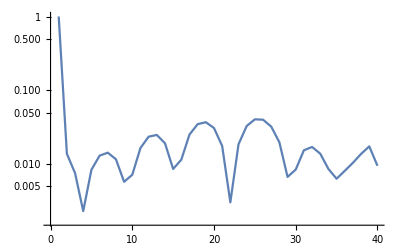
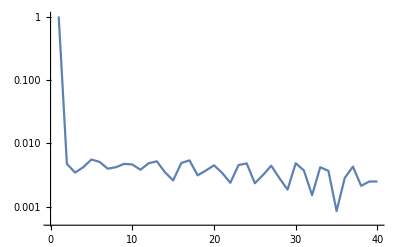
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
DCTPlot/@Grhp1
```

#### Compare with finite difference method

```mathematica
xmin=-5;
xmax=5;
dx=1.;
tmin=0.;
tmax=2;
dt=1;
lmax=10.//N;
```

```mathematica
(*FD solve nonlinear eq*)
FDsolver[NN_]:=Module[{},
ddt=1/NN/2;
ddx=1/NN;
xxx=Range[-lmax,lmax-ddx,ddx];
ttt=Range[tmin,tmax,ddt];
nq0=Table[q[x],{x,-lmax,lmax-ddx,ddx}];(*even number of points*)
nqt0=Table[qt[x],{x,-lmax,lmax-ddx,ddx}];(*even number of points*)
nx=Round[2*lmax/ddx]; 
nt=Round[tmax/ddt]+1;
qfd=ConstantArray[0,{nx,nt}];
For[j=1,j≤nx,j=j+1,
qfd[[j,1]]=nq0[[j]];
qfd[[j,2]]=nq0[[j]]+nqt0[[j]]*ddt;
];
For[n=1,n≤ nt-2,n++,
For[j=2,j≤nx-1,j=j+1,
qfd[[j,n+2]]=(ddt/ddx)^2*(qfd[[j+1,n+1]]-2qfd[[j,n+1]]+qfd[[j-1,n+1]])-ddt^2*Sin[qfd[[j,n+1]]]+2qfd[[j,n+1]]-qfd[[j,n]]
]
];
iqfd=Interpolation[Flatten[Table[{{xxx[[j]],ttt[[n]]},qfd[[j,n]]},{j,1,nx},{n,1,nt}],1]];
{qfd,iqfd}
]
```

```mathematica
Timing[qfd=FDsolver[10][[1]]][[1]]
```

0.09375

```mathematica
(*plot fd sol*)
Manipulate[
{ListLinePlot[Cases[Table[{xxx[[k]],Re[Cos[qfd[[k,t]]]]},{k,1,nx,Round[nx/200]+1}],{x_,y_}/;-lmax≤x≤lmax],PlotRange->{-1,1}],ListLinePlot[Cases[Table[{xxx[[k]],Re[qfd[[k,t]]]},{k,1,nx,Round[nx/200]+1}],{x_,y_}/;-lmax≤x≤lmax],PlotRange->All]},{t,1,nt,Round[nt/30]+1}]
```

```mathematica
(*plot interpolated fd sol*)
Manipulate[TablePlot[Cos[iqfd[x,t]],{x,xmin,xmax,dx},PlotRange->{-1,1},InterpolationOrder->1,PlotStyle->Thick],{t,tmin,tmax,dt}]
```

```mathematica
(*compute ist sol*)
Monitor[qSGm=Table[qSG[x,t],{x,xmin,xmax,dx},{t,tmin,tmax,dt}],timestring];
Save[qSGgeneral,qSGm];
```

```mathematica
(*no monitor version*)
qSGm=Table[qSG[x,tt],{x,xmin,xmax,dx},{tt,tmin,tmax,dt}];
Save[qSGgeneral,qSGm];
```

```mathematica
ix=Range[xmin,xmax,dx];
it=Range[tmin,tmax,dt];
icosq=Interpolation[Flatten[Table[{{ix[[j]],it[[n]]},(qSGm[[j,n]].{{1,0},{0,-1}}.Inverse[qSGm[[j,n]]])[[1,1]]},{j,1,Length[ix]},{n,1,Length[it]}],1]];
```

Interpolation::inhr: Requested order is too high; order has been reduced to {3,2}.

```mathematica
(*plot ist sol*)
Manipulate[
TablePlot[Re[icosq[x,t]],{x,xmin,xmax,dx},PlotRange->{-1,1},InterpolationOrder->1,PlotStyle->Thick],{t,tmin,tmax,dt}]
```

```mathematica
iqfd10=FDsolver[10][[2]];
iqfd20=FDsolver[20][[2]];
iqfd40=FDsolver[40][[2]];
iqfd80=FDsolver[80][[2]];
iqfd160=FDsolver[160][[2]];
```

```mathematica
(*difference between fd and ist*)
Manipulate[
{TablePlot[{icosq[x,t],Cos[iqfd10[x,t]]},{x,xmin,xmax,dx},PlotRange->{-1.1,1.1},InterpolationOrder->1,PlotStyle->Thick],TablePlot[Abs[icosq[x,t]-Cos[iqfd10[x,t]]],{x,xmin,xmax,dx},PlotRange->All,InterpolationOrder->1,PlotStyle->Thick],
TablePlot[Abs[icosq[x,t]-Cos[iqfd20[x,t]]],{x,xmin,xmax,dx},PlotRange->All,InterpolationOrder->1,PlotStyle->Thick],
TablePlot[Abs[icosq[x,t]-Cos[iqfd40[x,t]]],{x,xmin,xmax,dx},PlotRange->All,InterpolationOrder->1,PlotStyle->Thick],
TablePlot[Abs[icosq[x,t]-Cos[iqfd80[x,t]]],{x,xmin,xmax,dx},PlotRange->All,InterpolationOrder->1,PlotStyle->Thick],
TablePlot[Abs[icosq[x,t]-Cos[iqfd160[x,t]]],{x,xmin,xmax,dx},PlotRange->All,InterpolationOrder->1,PlotStyle->Thick]},{t,tmin,tmax,dt}]
```

```mathematica
(*solve linearized eq  utt-uxx+u=0*)
Manipulate[
dd=0.2;
xx=Range[-lmax,lmax-dd,dd];
nq0=Table[q[x],{x,-LL,LL-dd,dd}];(*even number of points*)
nqt0=Table[qt[x],{x,-LL,LL-dd,dd}];(*even number of points*)
w=Pi/LL*Join[Range[0,Length[nq0]/2], Range[-Length[nq0]/2+1,-1]];
nhq0=Fourier[nq0];
nhqt0=Fourier[nqt0];
(*nhqt=Quiet[nhq0*Exp[I/w*tt]*I*w/.Indeterminate->0.];*)
nhqt=(nhq0*Cos[Sqrt[1+w^2]*tt]+nhqt0/Sqrt[1+w^2]*Sin[Sqrt[1+w^2]*tt])/.Indeterminate->0.;
nqt=InverseFourier[nhqt];
ListLinePlot[Cases[Table[{xx[[k]],Cos[Re[nqt[[k]]]]},{k,1,Length[nq0]}],{x_,y_}/;-LL≤x≤LL],PlotRange->{-1,1}],{tt,0,10,0.1/8}]
```

### Debug

```mathematica
ListPlot3D[Flatten[Table[{x,y,Abs[G[0,0][x+I y][[1,2]]]},{x,-1/2,1/2,0.1},{y,-1/2,1/2,0.1}],1],AxesLabel->{x,y,z},PlotRange->All]
```

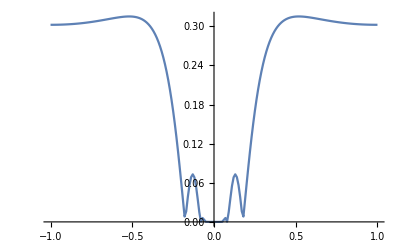

```mathematica
TablePlot[Abs[G[0,0][z][[2,1]]],{z,-1,1,0.01},PlotRange->All]
```

```mathematica
{out,phi,rhp1,rhp2,tt}=SG[0][0,0];
```

Private`PoleList[0,0]

```mathematica
out
```

{{1.-2.61924×10^-17 ⅈ,-9.07193×10^-7+1.61446×10^-14 ⅈ},{1.05074×10^-6+1.38608×10^-14 ⅈ,1.-3.20662×10^-17 ⅈ}}

```mathematica
phi[0]
```

{{1.-2.61924×10^-17 ⅈ,-9.07193×10^-7+1.61446×10^-14 ⅈ},{1.05074×10^-6+1.38608×10^-14 ⅈ,1.-3.20662×10^-17 ⅈ}}

```mathematica
rhp2
```

Private`rhp2$8428

```mathematica
RHSolved//Clear;
RHSolved[X_]:=RHSolved[X]=RHSolve[X];
RHSolved[{}]:=0.;
RHSolution[X_][z_]:=Cauchy[X//RHSolved,z]+IdentityMatrix[2];
```

```mathematica
RHSolution[rhp1][0]
```

{{0.540253-2.41751×10^-14 ⅈ,-0.84145+1.80897×10^-14 ⅈ},{0.841514+1.52933×10^-14 ⅈ,0.540317+2.72282×10^-14 ⅈ}}

```mathematica
RHSolution[rhp2][0]
```

{{1+Cauchy[0.,0],Cauchy[0.,0]},{Cauchy[0.,0],1+Cauchy[0.,0]}}

```mathematica
r[k_]:=ρ[k];
θ[x_,t_][z_]:=2 I (-t/4/z+x z);
rb[k_]:= cc[r[cc[k]]];
rbsamp[k_]:= cc[rsamp[cc[k]]];
τsamp[k_]:=1+ rsamp[k]cc[rsamp[cc[k]]];

G[x_,t_][z_]:=({{1+r[z]rb[z], rb[z]Exp[-θ[x,t][k]]}, {r[z] Exp[θ[x,t][k]], 1}});
G[_,_][_?InfinityQ]:=({{1., 0}, {0, 1.}});
```

```mathematica
J[0][0,0]
```

{{G[0,0][#1]&,G[0,0][#1]&},{Line[{-100,0}],Line[{0,100}]},{40,40}}

```mathematica
J[1][-10,0]
```

{{U[-10,0][#1]&,U[-10,0][#1]&,Private`DD[#1]&,L[-10,0][#1]&,L[-10,0][#1]&,Private`P[-10,0][#1]&,Private`P[-10,0][#1]&,Private`M[-10,0][#1]&,Private`M[-10,0][#1]&},{Line[{0.+0.4 ⅈ,99.6+0.4 ⅈ}],Line[{99.6+0.4 ⅈ,100}],Line[{0,100}],Line[{0.-0.4 ⅈ,99.6-0.4 ⅈ}],Line[{99.6-0.4 ⅈ,100}],Line[{100,100.4+0.4 ⅈ}],Line[{100.4+0.4 ⅈ,200.+0.4 ⅈ}],Line[{100,100.4-0.4 ⅈ}],Line[{100.4-0.4 ⅈ,200.-0.4 ⅈ}]},{20,20,20,20,20,20,20,20,20}}

```mathematica
Jadapt[1][-10,0]
```

{{U[-10,0][#1]&,Private`DD[#1]&,L[-10,0][#1]&},{Line[{0.+0.4 ⅈ,7.9125+0.4 ⅈ}],Line[{0,5.8625}],Line[{0.-0.4 ⅈ,7.9125-0.4 ⅈ}]},{40,40,40}}

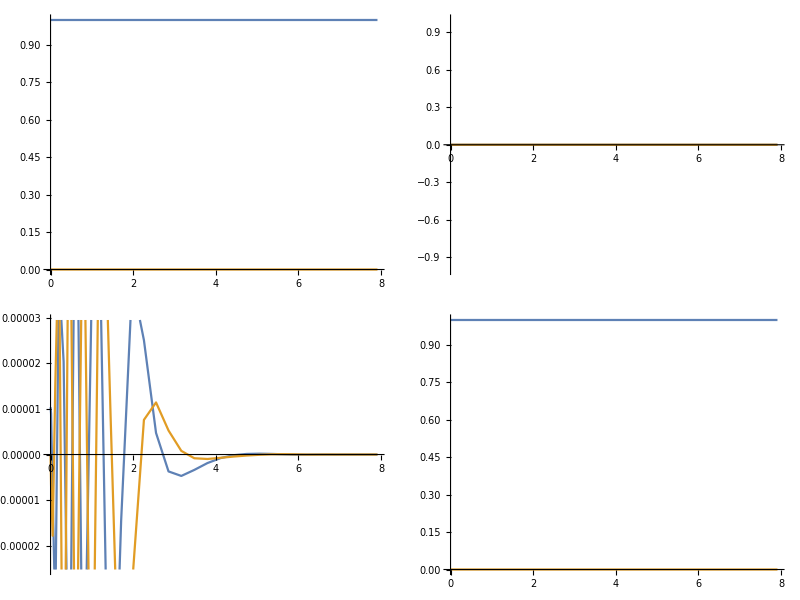
(-Graphics-)

```mathematica
ff=Fun[L[-10,0][#1]&,Line[{0.-0.4 ⅈ,7.912499999999998-0.4 ⅈ}],40]
```

```mathematica
L[-10,0][0]
```

{{1,0},{0.499885,1}}

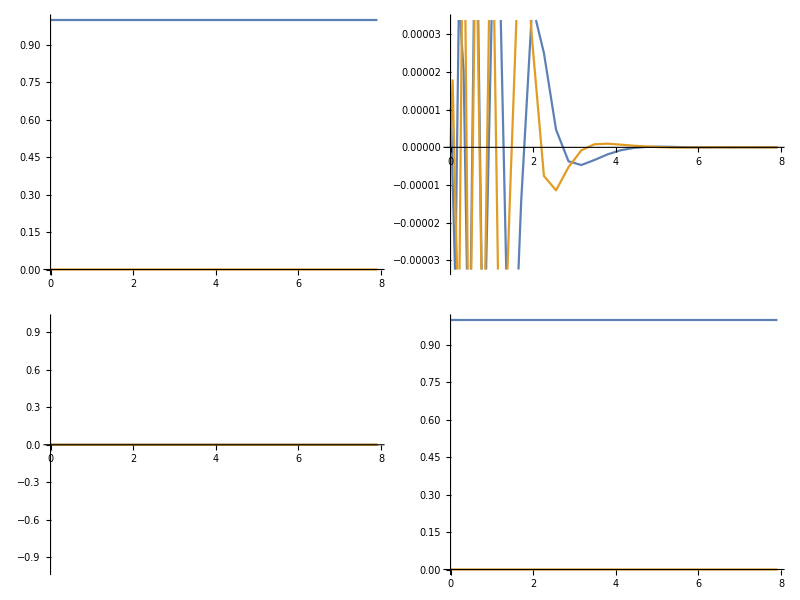
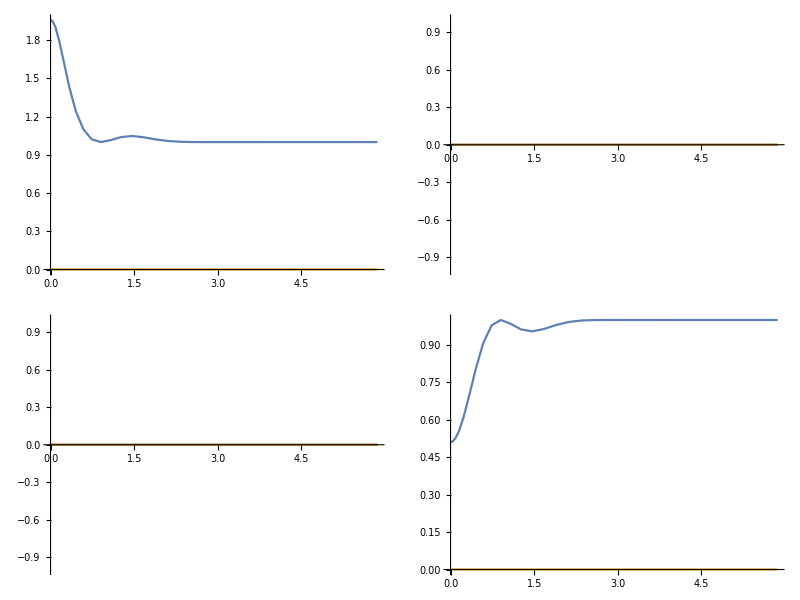
{(-Graphics-),(-Graphics-),(-Graphics-)}

```mathematica
GG=Jadapt[1][-10,0]//MakeListFun
```

```mathematica
Grhp1[[1]][-1]
```

{{1.+2.71019×10^-8 ⅈ,-13985.2-18010.7 ⅈ},{0.+0. ⅈ,1.+1.49136×10^-8 ⅈ}}

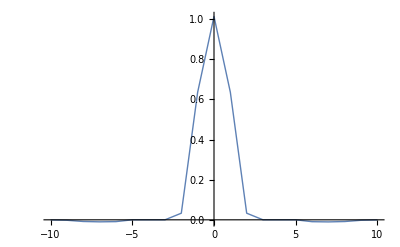

```mathematica
(* Focusing *)
Monitor[TablePlot[qNLS[x,0.0]//Re,{x,-10,10,1.},PlotRange->All,InterpolationOrder->1,PlotStyle->Thick],timestring]
```

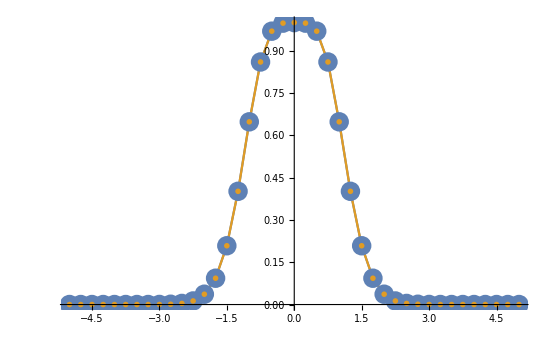

```mathematica
TablePlot[{qNLS[x,0.]//Re,Sech[x^2]},{x,-10,10,1.},PlotMarkers->{{●,20},{"x",30}}]
```

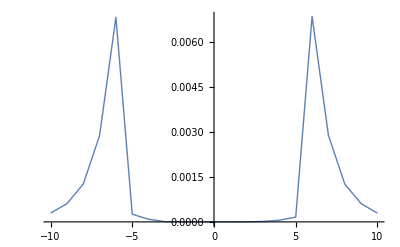

```mathematica
TablePlot[Abs[qNLS[x,0.]-Sech[x^2]],{x,-10,10,1.},PlotRange->All,InterpolationOrder->1,PlotStyle->Thick]
```

```mathematica
TablePlot[Abs[qNLS[x,0.0]-Sech[x^2]]/Sech[x^2],{x,-10,10,1.},PlotRange->All,InterpolationOrder->1,PlotStyle->Thick]
```

```mathematica
(* Defocusing *)
Monitor[TablePlot[qmKdV[x,1.]//Re,{x,-20,10,.25},PlotRange->All,InterpolationOrder->1,PlotStyle->Thick],timestring]
```

$Aborted

RuleDelayed::rhs: Pattern mu_ appears on the right-hand side of rule pp[mu_,nn_]:>(pp[mu_,nn_]=LocatePolesSG[q,qx,qt,mu,nn]).

RuleDelayed::rhs: Pattern nn_ appears on the right-hand side of rule pp[mu_,nn_]:>(pp[mu_,nn_]=LocatePolesSG[q,qx,qt,mu,nn]).

$Aborted

LinearSolve::matrix: Argument {{«1»}+{(0.+0.000510204 ⅈ) (-1/Part[«2»]+{}⟦2⟧),(0.-0.00102041 ⅈ) (-1/Part[«2»]+{}⟦2⟧),(0.+0.00102041 ⅈ) (-1/Part[«2»]+{}⟦2⟧),(0.-0.00102041 ⅈ) (-1/Part[«2»]+{}⟦2⟧),«44»,(0.+0.00102041 ⅈ) (-1/Part[«2»]+{}⟦2⟧),(0.-0.000510204 ⅈ) (-1/Part[«2»]+{}⟦2⟧),«50»},«49»,«50»} at position 1 is not a non-empty rectangular matrix.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0. π ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0. π ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. π ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Part::partw: Part 50 of LinearSolve[{{1-{«50»}.DiagonalMatrix[«1»],«49»,«1»}+{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,«50»},{«1»}+{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,«50»},«47»,{«1»}+{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,«17»,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,«50»},«50»},«1»] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

LinearSolve::matrix: Argument {{«1»}+{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,«50»},«49»,«50»} at position 1 is not a non-empty rectangular matrix.

General::stop: Further output of LinearSolve::matrix will be suppressed during this calculation.

Inverse::matsq: Argument {{{«1»},{{1-Dot[«2»],-{«50»}.DiagonalMatrix[«1»],-{«50»}.DiagonalMatrix[«1»],-{«50»}.DiagonalMatrix[«1»],-{«50»}.DiagonalMatrix[«1»],-{«50»}.DiagonalMatrix[«1»],-{«50»}.DiagonalMatrix[«1»],«38»,-{«50»}.DiagonalMatrix[«1»],-{«50»}.DiagonalMatrix[«1»],-{«50»}.DiagonalMatrix[«1»],-{«50»}.DiagonalMatrix[«1»],-{«50»}.DiagonalMatrix[«1»],«1»}+{«1»},«49»,«50»}},{«1»⟦51⟧,«1»}} at position 1 is not a non-empty square matrix.

$Aborted[]